```mathematica
NotebookSave[];
```

## Init

### Form factors

```mathematica
(* Formfactor definition and values from [1811.00983] *)
```

```mathematica
tplus[mK_]:=(mB+mK)^2;
tminus[mK_]:=(mB-mK)^2;
tzero[mK_]:=tplus[mK](1-Sqrt[1-tminus[mK]/tplus[mK]]);
```

```mathematica
zz[t_,mK_]:=(Sqrt[tplus[mK]-t]-Sqrt[tplus[mK]-tzero[mK]])/(Sqrt[tplus[mK]-t]+Sqrt[tplus[mK]-tzero[mK]]);
```

```mathematica
FF[q.b2_,x_,mK_]:=1/(1-(q.b2)/Subscript[m, R,x]^2)Sum[Subscript[α, k,x](zz[q.b2,mK]-zz[0,mK])^k,{k,0,2}]/.formFactors/.values/.masses/.couplings/.ckms;
```

```mathematica
V0AB[q.b2_,F0_,aAB_,bAB_]:= F0/(1-aAB (q.b2)/mB^2+bAB((q.b2)/mB^2)^2)/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
(* we need f0 and f+ only for the B->K pseudoscalar decay, but A0 for B->K^* vector decays for different K^* masses, so we explicitly have to add mP (or mK^*) here *)
```

```mathematica
(* all masses (and mass-dimension quantities) in GeV units *)
```

```mathematica
constants = {GevToInverseSec :> 1.5 10^24};
values={Subscript[α, 0,fzero]:>0.329, Subscript[α, 1,fzero]:>0.195,Subscript[α, 2,fzero]:>-0.446,Subscript[α, 0,fplus]:>0.329,Subscript[α, 1,fplus]:>-0.876,Subscript[α, 2,fplus]:>0.006,Subscript[α, 0,Azero]:>0.343,Subscript[α, 1,Azero]:>-1.130,Subscript[α, 2,Azero]:>2.326,Subscript[m, R,fzero]:>5.54 , Subscript[m, R,fplus]:>5.325 ,Subscript[m, R,Azero]:>5.279,F0BS700:>0.46, aS700:>1.6,bS700:>1.35 ,F0BS1430:>0.17, aS1430:>4.4,bS1430:>6.4 ,F0A:>0.22, F0B:>-0.45,aA:>2.4,aB:>1.34,bA:>1.78,bB:>0.69,ΘK1:>-34 Degree,mK1A:>1.31,mK1B:>1.34,V012700:>-0.52,V01400:>-0.07};
```

```mathematica
V0BK1270func[q.b2_]:=1/1.270(Sin[ΘK1] mK1A V0AB[q.b2,F0A,aA,bA]+Cos[ΘK1] mK1B V0AB[q.b2,F0B,aB,bB])/.values
V0BK1400func[q.b2_]:=1/1.4(Cos[ΘK1] mK1A V0AB[q.b2,F0A,aA,bA]-Sin[ΘK1] mK1B V0AB[q.b2,F0B,aB,bB])/.values
```

```mathematica
formFactors={fplus[q.b2_,F0_,a_,b_]:> V0AB[q.b2,F0,a,b],V0BK1270[q.b2_]:>V0BK1270func[q.b2] ,V0BK1400[q.b2_]:>V0BK1400func[q.b2] , fzero[q.b2_]:> FF[q.b2,fzero,mK],Azero[qsqr_,mP_]:>FF[qsqr,Azero,mP]};
```

### Masses and couplings

```mathematica
τB=1.638;(*ps*)
ΓtotalB=6.582*10^-25/(10^-12 τB);(*GeV*)
cτB=3 10^10 10^-12 τB(*in cm*);
```

```mathematica
masses={MW:>80.38,mW:>80.38,MZ:>91.19,mZ:>91.19,v:>246,vev:>246,Γh:>0.013,MT:>173,mt:>173,MC:>1.28,mc:>1.28,MU:>0.0022,mu:>0.0022,MB:>4.18,mb:>4.18,MS:>0.095,ms:>0.095,MD:>0.0047,md:>0.0047,mτ:>1.777,mμ:>0.106,me:>0.000511,mBs:>5.367,mBd:>5.280,mB:>5.279,mD:>1.86,mK:>0.4937, mKstarV892:>0.892, mKstarV1410:>1.41, mKstarV1680:>1.72,mKAV1270:>1.27,mKAV1400:>1.4,mKstarS700:>0.7,mKstarS1430:>1.43,mπ:>0.14,fBs:>0.227,fBd:>0.188};
ckms={CKM[3,3]:>1,Vtb:>1,CKM[3,2]:>39.4/1000,Vts:>39.4/1000,CKM[3,1]:>8.1/1000, Vtd:> 8.1/1000,CKM[2,3]:>42.2/1000,Vcb:>42.2/1000,CKM[2,2]:>0.997,Vcs:>0.997,CKM[2,1]:>0.218,Vcd:>0.218,CKM[1,3]:>3.94/1000,Vub:>3.94/1000,CKM[1,2]:>0.2243,Vus:>0.2243,CKM[1,1]:>0.9742,Vud:>0.9742}; 
(* PDG values, but Vtb is there actually 1.019±0.025 which we reduce to an exact 1 here *)
couplings={EL:>Sqrt[4 π*7.297/1000],SW:>Sqrt[0.231],CW:>Sqrt[1-0.231],GF:>1.166*10^(-5),Subscript[α,em]:>7.297*10^-3,alphaem:>7.297*10^-3,alphas:>0.1181};
```

### Γϕ

```mathematica
SetDirectory[ NotebookDirectory[]];
```

```mathematica
datapointsππ=ReadList[File["current/rate_pipi.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

```mathematica
datapointsππ//InputForm
```

{{0.27, 0.}, {0.2712462633751667, 0.}, {0.2724982792407048, 0.}, {0.27375607414890346, 0.}, {0.2750196747746116, 0.}, {0.27628910791580363, 0.}, 
 {0.2775644004941479, 0.}, {0.27884557955557737, 0.}, {0.28013267227086347, 5.672232559058714*^-10}, {0.28142570593619215, 8.862240771159831*^-10}, 
 {0.28272470797374294, 1.1262327807181056*^-9}, {0.2840297059322702, 1.3296468463979139*^-9}, {0.28534072748768785, 1.5106515473967013*^-9}, 
 {0.2866578004436557, 1.6761978417186815*^-9}, {0.28798095273216967, 1.8304719679116536*^-9}, {0.2893102124141538, 1.976393120194482*^-9}, 
 {0.2906456076800555, 2.1162121855277224*^-9}, {0.2919871668504433, 2.2517622497876735*^-9}, {0.29333491837660775, 2.3841014455405747*^-9}, 
 {0.29468889084116434, 2.5139200224668937*^-9}, {0.29604911295866, 2.6417269012483123*^-9}, {0.2974156135761821, 2.7678936896843348*^-9}, 
 {0.29878842167396996, 2.89268527716951*^-9}, {0.3001675663660297, 3.016106410409919*^-9}, {0.30155307690075156, 3.137169008252768*^-9}, 
 {0.3029449826615302, 3.2573213115098304*^-9}, {0.3043433131673879, 3.3767695265924426*^-9}, {0.3057480980736005, 3.4956965755989106*^-9}, 
 {0.3071593671723264, 3.6142665197776493*^-9}, {0.3085771503932384, 3.732628023668245*^-9}, {0.31000147780415843, 3.850919039053553*^-9}, 
 {0.31143237961169495, 3.972048943183302*^-9}, {0.3128698861618841, 4.093122829629923*^-9}, {0.31431402794083274, 4.2138485286982135*^-9}, 
 {0.3157648355753652, 4.333886634600289*^-9}, {0.31722233983367304, 4.452852699976383*^-9}, {0.31868657162596703, 4.570318452258739*^-9}, 
 {0.3201575620051333, 4.6846742217258994*^-9}, {0.32163534216739126, 4.787127670637974*^-9}, {0.3231199434529558, 4.887778474827764*^-9}, 
 {0.3246113973467015, 4.987642820336092*^-9}, {0.3261097354788307, 5.087824803359941*^-9}, {0.3276149896255439, 5.189516755736039*^-9}, 
 {0.329127191709714, 5.2940009096032844*^-9}, {0.33064637380156314, 5.409875459591465*^-9}, {0.33217256811934304, 5.540517151307265*^-9}, 
 {0.33370580703001784, 5.6754015428596224*^-9}, {0.335246123049951, 5.813476019810257*^-9}, {0.33679354884559465, 5.953577496305441*^-9}, 
 {0.33834811723418234, 6.0944294303199995*^-9}, {0.3399098611844252, 6.234657026834364*^-9}, {0.3414788138172109, 6.357436642565181*^-9}, 
 {0.34305500840630626, 6.47740172587304*^-9}, {0.34463847837906286, 6.596433503562995*^-9}, {0.34622925731712584, 6.71556846427926*^-9}, 
 {0.3478273789571462, 6.835920640494966*^-9}, {0.34943287719149624, 6.958682638685085*^-9}, {0.3510457860689884, 7.094538746743879*^-9}, 
 {0.35266613979559724, 7.239405846662604*^-9}, {0.35429397273518487, 7.387186780174108*^-9}, {0.3559293194102299, 7.536783014896522*^-9}, 
 {0.3575722145025595, 7.687007396655421*^-9}, {0.35922269285408465, 7.836582695677489*^-9}, {0.36088078946753943, 7.975655253547748*^-9}, 
 {0.36254653950722326, 8.104873143791936*^-9}, {0.3642199782997465, 8.23295455930727*^-9}, {0.3659011413347798, 8.361284005920816*^-9}, 
 {0.36759006426580654, 8.49133767985187*^-9}, {0.3692867829108793, 8.624685077241024*^-9}, {0.3709913332533792, 8.772345424823138*^-9}, 
 {0.37270375144277895, 8.932133802580257*^-9}, {0.37442407379540993, 9.096219457391776*^-9}, {0.3761523367952319, 9.263383835239694*^-9}, 
 {0.37788857709460694, 9.432319163430822*^-9}, {0.3796328315150768, 9.601626182486191*^-9}, {0.38138513704814375, 9.75910291117647*^-9}, 
 {0.38314553085605496, 9.912760758339246*^-9}, {0.38491405027259085, 1.0066517305255376*^-8}, {0.3866907328038568, 1.0221491281420968*^-8}, 
 {0.3884756161290783, 1.0378868611211071*^-8}, {0.3902687381014005, 1.0541117361080796*^-8}, {0.3920701367486905, 1.0714946442489598*^-8}, 
 {0.39387985027434413, 1.0893450572064205*^-8}, {0.3956979170580962, 1.1076381640947466*^-8}, {0.3975243756568342, 1.126347109538128*^-8}, 
 {0.3993592648054161, 1.1454429214663815*^-8}, {0.40120262341749197, 1.164866247213669*^-8}, {0.40305449058632903, 1.1846021645782072*^-8}, 
 {0.40491490558564086, 1.2046394404321485*^-8}, {0.40678390787042035, 1.2249497296225197*^-8}, {0.40866153707777625, 1.245502649980676*^-8}, 
 {0.41054783302777387, 1.2664051989754778*^-8}, {0.41244283572427964, 1.2877965508551299*^-8}, {0.41434658535580954, 1.3091992405316315*^-8}, 
 {0.41625912229638107, 1.3304589881881625*^-8}, {0.41818048710637, 1.3514122378525677*^-8}, {0.4201107205333701, 1.3717704316844245*^-8}, 
 {0.4220498635130577, 1.3896303126950565*^-8}, {0.4239979571700592, 1.4070967063487669*^-8}, {0.4259550428188242, 1.4244658050603248*^-8}, 
 {0.4279211619645007, 1.442050634409966*^-8}, {0.429896356303816, 1.4601813128844435*^-8}, {0.4318806677259606, 1.4808826908716952*^-8}, 
 {0.43387413831347693, 1.5025573986710564*^-8}, {0.43587681034315134, 1.5250339409141818*^-8}, {0.4378887262869111, 1.5482298181987035*^-8}, 
 {0.43990992881272506, 1.572055701942013*^-8}, {0.44194046078550836, 1.5968167286545848*^-8}, {0.4439803652680316, 1.6219289452209027*^-8}, 
 {0.4460296855218341, 1.6471498477890674*^-8}, {0.44808846500814137, 1.6722436655388963*^-8}, {0.45015674738878697, 1.69678426048306*^-8}, 
 {0.4522345765271381, 1.718618864843255*^-8}, {0.4543219964890262, 1.7401855695159886*^-8}, {0.45641905154368134, 1.7618572753063138*^-8}, 
 {0.458525786164671, 1.784024730365145*^-8}, {0.4606422450308434, 1.8080721401279035*^-8}, {0.46276847302727486, 1.8354214754148875*^-8}, 
 {0.46490451524622195, 1.8634313757034006*^-8}, {0.4670504169880775, 1.8916224420587444*^-8}, {0.4692062237623314, 1.91948952719071*^-8}, 
 {0.4713719812885361, 1.944241110356225*^-8}, {0.4735477354972756, 1.9668700046633094*^-8}, {0.4757335325311399, 1.9891921749006097*^-8}, 
 {0.47792941874570377, 2.0117305885681385*^-8}, {0.48013544071050923, 2.0352030193423225*^-8}, {0.48235164521005375, 2.0624787645278063*^-8}, 
 {0.48457807924478224, 2.090844513249127*^-8}, {0.48681479003208367, 2.1200516838802272*^-8}, {0.4890618250072927, 2.1498376804411856*^-8}, 
 {0.4913192318246956, 2.17997772020148*^-8}, {0.4935870583585406, 2.2101507517155963*^-8}, {0.49586535270405363, 2.239982504011456*^-8}, 
 {0.49815416317845795, 2.2691183217239486*^-8}, {0.5004535383219991, 2.2965174165751374*^-8}, {0.5027635268989743, 2.3200078992025646*^-8}, 
 {0.5050841778987663, 2.3429280446364417*^-8}, {0.5074155405368825, 2.3660275655830387*^-8}, {0.5097576642559993, 2.3900895254825147*^-8}, 
 {0.5121105987270096, 2.4186255690485288*^-8}, {0.5144743938500769, 2.4492114447863825*^-8}, {0.5168490997556933, 2.481318986405827*^-8}, 
 {0.5192347668057429, 2.514731583864308*^-8}, {0.5216314455945695, 2.549682577663495*^-8}, {0.5240391869500503, 2.5855353290057326*^-8}, 
 {0.5264580419346723, 2.6215656230829443*^-8}, {0.5288880618466173, 2.6572445239085817*^-8}, {0.5313292982208482, 2.691070956397661*^-8}, 
 {0.5337818028302025, 2.7229540607155872*^-8}, {0.5362456276864903, 2.7537482865556885*^-8}, {0.5387208250415976, 2.7835134955816618*^-8}, 
 {0.5412074473885936, 2.811381457085649*^-8}, {0.5437055474628448, 2.8376865529523696*^-8}, {0.5462151782431334, 2.8642181208311465*^-8}, 
 {0.5487363929527799, 2.891827453734363*^-8}, {0.551269245060773, 2.923629523434285*^-8}, {0.5538137882829027, 2.959713691822173*^-8}, 
 {0.5563700765829002, 2.997036260937804*^-8}, {0.5589381641735814, 3.0347192348679216*^-8}, {0.5615181055179979, 3.069936336776339*^-8}, 
 {0.5641099553305907, 3.1030405280083985*^-8}, {0.5667137685783515, 3.135758103575526*^-8}, {0.5693296004819882, 3.168485308209693*^-8}, 
 {0.5719575065170955, 3.2015813582594334*^-8}, {0.5745975424153323, 3.2355189361859084*^-8}, {0.5772497641656028, 3.270794590479613*^-8}, 
 {0.5799142280152443, 3.3079104037720106*^-8}, {0.58259099047122, 3.35085259791105*^-8}, {0.5852801083013177, 3.395300989804619*^-8}, 
 {0.587981638535353, 3.4399857139509577*^-8}, {0.5906956384663793, 3.482676690938912*^-8}, {0.5934221656519029, 3.520694936332948*^-8}, 
 {0.5961612779151031, 3.5573894686832796*^-8}, {0.5989130333460593, 3.593294617412031*^-8}, {0.6016774903029821, 3.628920713450654*^-8}, 
 {0.6044547074134519, 3.6648842501472193*^-8}, {0.6072447435756609, 3.701857169213708*^-8}, {0.610047657959664, 3.740541360294682*^-8}, 
 {0.6128635100086319, 3.783738270952246*^-8}, {0.6156923594401129, 3.828884166902632*^-8}, {0.6185342662472988, 3.875560914313004*^-8}, 
 {0.6213892907002974, 3.9238452655587105*^-8}, {0.6242574933474107, 3.9730869401098054*^-8}, {0.6271389350164189, 4.0217350299569713*^-8}, 
 {0.6300336768158707, 4.068645892613893*^-8}, {0.632941780136379, 4.106636140072195*^-8}, {0.6358633066519227, 4.144059060652708*^-8}, 
 {0.6387983183211547, 4.183277474247722*^-8}, {0.6417468773887167, 4.2317514770378834*^-8}, {0.644709046386558, 4.2879612258907114*^-8}, 
 {0.6476848881352625, 4.346429996316916*^-8}, {0.6506744657453807, 4.403915294938765*^-8}, {0.6536778426187682, 4.456217235236772*^-8}, 
 {0.6566950824499302, 4.507549073110715*^-8}, {0.6597262492273724, 4.558447684321061*^-8}, {0.6627714072349583, 4.609140078380415*^-8}, 
 {0.6658306210532717, 4.6606968441722975*^-8}, {0.6689039555609871, 4.7139869697261996*^-8}, {0.6719914759362456, 4.7712054595502816*^-8}, 
 {0.6750932476580366, 4.8318991226229124*^-8}, {0.6782093365075867, 4.894990185872476*^-8}, {0.6813398085697553, 4.9599303196337625*^-8}, 
 {0.6844847302344351, 5.026442552384142*^-8}, {0.6876441681979611, 5.094761823039026*^-8}, {0.6908181894645244, 5.164761436396743*^-8}, 
 {0.6940068613475934, 5.236292075941782*^-8}, {0.6972102514713411, 5.309632369690118*^-8}, {0.7004284277720799, 5.3847477907313915*^-8}, 
 {0.703661458499702, 5.461157019119484*^-8}, {0.7069094122191261, 5.540354436403315*^-8}, {0.7101723578117531, 5.623357612623065*^-8}, 
 {0.7134503644769257, 5.71466815386731*^-8}, {0.7167435017333957, 5.807974789784948*^-8}, {0.7200518394207996, 5.9007801649435984*^-8}, 
 {0.7233754477011387, 5.983558367617379*^-8}, {0.7267143970602673, 6.066350928687997*^-8}, {0.7300687583093879, 6.152260578113352*^-8}, 
 {0.7334386025865524, 6.249510738631665*^-8}, {0.736824001358171, 6.351930345643758*^-8}, {0.7402250264205283, 6.458331665004307*^-8}, 
 {0.743641749901305, 6.564863687014202*^-8}, {0.7470742442611082, 6.676622704193298*^-8}, {0.750522582295008, 6.796521248930887*^-8}, 
 {0.7539868371340813, 6.930050645841937*^-8}, {0.7574670822469628, 7.069454633815442*^-8}, {0.7609633914414027, 7.210224085616296*^-8}, 
 {0.7644758388658325, 7.348021006876173*^-8}, {0.7680044990109374, 7.488114305748583*^-8}, {0.7715494467112358, 7.631450591440702*^-8}, 
 {0.7751107571466667, 7.779625141669429*^-8}, {0.7786885058441837, 7.935409666198095*^-8}, {0.7822827686793573, 8.105493062780866*^-8}, 
 {0.7858936218779836, 8.287401694527475*^-8}, {0.7895211420177007, 8.475607847498655*^-8}, {0.7931654060296135, 8.659839496079167*^-8}, 
 {0.7968264911999243, 8.848674314919715*^-8}, {0.8005044751715726, 9.047851260955996*^-8}, {0.8041994359458814, 9.263762806963812*^-8}, 
 {0.8079114518842112, 9.49442979434633*^-8}, {0.8116406017096225, 9.743363394521041*^-8}, {0.8153869645085444, 1.0010800187171046*^-7}, 
 {0.8191506197324531, 1.029097051712941*^-7}, {0.8229316471995555, 1.0574828671037758*^-7}, {0.826730127096483, 1.0867806326198211*^-7}, 
 {0.8305461399799913, 1.1175405439084912*^-7}, {0.8343797667786695, 1.1502200268847181*^-7}, {0.8382310887946561, 1.1850086959869701*^-7}, 
 {0.8421001877053631, 1.222415657603768*^-7}, {0.8459871455652082, 1.2625755119697302*^-7}, {0.8498920448073554, 1.305348379636435*^-7}, 
 {0.8538149682454625, 1.350486337710003*^-7}, {0.8577559990754382, 1.3986482813104436*^-7}, {0.8617152208772058, 1.4507826911731205*^-7}, 
 {0.8656927176164758, 1.5069350407118297*^-7}, {0.8696885736465274, 1.565582048997267*^-7}, {0.8737028737099964, 1.6221386488386454*^-7}, 
 {0.8777357029406729, 1.6831857961678226*^-7}, {0.8817871468653068, 1.7559402754346634*^-7}, {0.8858572914054215, 1.8427536090305106*^-7}, 
 {0.889946222879136, 1.9380083113752742*^-7}, {0.894054028002996, 2.0362033976189195*^-7}, {0.8981807938938123, 2.1415622231983568*^-7}, 
 {0.9023266080705087, 2.255264582310907*^-7}, {0.9064915584559777, 2.3795165563997006*^-7}, {0.9106757333789461, 2.518305857354814*^-7}, 
 {0.914879221575847, 2.677146095318668*^-7}, {0.9191021121927025, 2.851753274135207*^-7}, {0.9233444947870141, 3.0371077101269597*^-7}, 
 {0.9276064593296617, 3.2398727628216504*^-7}, {0.931888096206812, 3.4715686434353925*^-7}, {0.9361894962218356, 3.7379088009514226*^-7}, 
 {0.940510750597232, 4.036217053581101*^-7}, {0.9448519509765648, 4.3711849402908656*^-7}, {0.9492131894264052, 4.742653436361843*^-7}, 
 {0.953594558438284, 5.170576539130732*^-7}, {0.9579961509306539, 5.636922952765069*^-7}, {0.9624180602508596, 6.16168812753588*^-7}, 
 {0.9668603801771175, 6.719139142532844*^-7}, {0.9713232049205044, 7.323315170259945*^-7}, {0.9758066291269561, 7.98204821217624*^-7}, 
 {0.9803107478792739, 8.043329987183871*^-7}, {0.9848356566991413, 6.566602972763539*^-7}, {0.98938145154915, 5.219949547567833*^-7}, 
 {0.9939482288348351, 4.361102230034945*^-7}, {0.998536085406719, 3.6369406807679374*^-7}, {1.003145118562366, 3.1400585460244836*^-7}, 
 {1.0077754260484457, 2.80400280725264*^-7}, {1.0124271060628058, 2.5206131557022364*^-7}, {1.0171002572565542, 2.262337933956374*^-7}, 
 {1.021794978736152, 2.0305536936573022*^-7}, {1.0265113700655153, 1.8188473983734485*^-7}, {1.0312495312681258, 1.6315942763753811*^-7}, 
 {1.0360095628291528, 1.468479918238075*^-7}, {1.040791565697584, 1.325663981264609*^-7}, {1.0455956412883665, 1.2015001841317736*^-7}, 
 {1.0504218914845578, 1.0907805659854005*^-7}, {1.0552704186394855, 9.895960832526572*^-8}, {1.0601413255789196, 8.988566298556252*^-8}, 
 {1.0650347156032518, 8.184875207118508*^-8}, {1.0699506924896867, 7.465859740346912*^-8}, {1.0748893604944427, 6.822253553261361*^-8}, 
 {1.0798508243549634, 6.237117567124722*^-8}, {1.084835189292138, 5.6834135375285026*^-8}, {1.0898425610125335, 5.193813217448053*^-8}, 
 {1.0948730457106364, 4.805373996984356*^-8}, {1.0999267500711045, 4.463212206590981*^-8}, {1.1050037812710294, 4.1227713175079316*^-8}, 
 {1.1101042469822102, 3.804940993633991*^-8}, {1.1152282553734358, 3.517482235660885*^-8}, {1.1203759151127801, 3.253874515185532*^-8}, 
 {1.1255473353699057, 3.010041194848091*^-8}, {1.1307426258183797, 2.791514245682761*^-8}, {1.1359618966379992, 2.602474854594541*^-8}, 
 {1.1412052585171282, 2.4219060767351058*^-8}, {1.146472822655045, 2.2389181303891808*^-8}, {1.1517647007643004, 2.0732576804915867*^-8}, 
 {1.1570810050730869, 1.9311407466440124*^-8}, {1.162421848327619, 1.805451831415412*^-8}, {1.1677873437945236, 1.6916827061404614*^-8}, 
 {1.1731776052632432, 1.5817276662966362*^-8}, {1.1785927470484483, 1.4772473087701153*^-8}, {1.1840328839924616, 1.3855647446346571*^-8}, 
 {1.189498131467694, 1.3059252421151808*^-8}, {1.194988605379092, 1.2373233553938791*^-8}, {1.2005044221665937, 1.1778828630111997*^-8}, 
 {1.2060456988076007, 1.1256094194707783*^-8}, {1.211612552819457, 1.078645007298555*^-8}, {1.2172051022619426, 1.036678426829665*^-8}, 
 {1.2228234657397763, 1.0072838960173768*^-8}, {1.2284677624051314, 9.895419403991737*^-9}, {1.2341381119601629, 9.725138805363296*^-9}, 
 {1.2398346346595455, 9.587003507713843*^-9}, {1.2455574513130245, 9.576364499060228*^-9}, {1.2513066832879778, 9.590887453241748*^-9}, 
 {1.2570824525119895, 9.552078621946237*^-9}, {1.2628848814754354, 9.628230329675673*^-9}, {1.268714093234082, 9.80829962864649*^-9}, 
 {1.2745702114116948, 9.846692486733752*^-9}, {1.2804533602026609, 9.889801576843478*^-9}, {1.2863636643746226, 1.0161949428734157*^-8}, 
 {1.2923012492711239, 1.0490326044720763*^-8}, {1.2982662408142673, 1.0804489640487701*^-8}, {1.3042587655073865, 1.1108903488654814*^-8}, 
 {1.3102789504377272, 1.1369557073636281*^-8}, {1.3163269232791435, 1.1533256828685666*^-8}, {1.322402812294805, 1.1657742543860143*^-8}, 
 {1.3285067463399178, 1.1756839292371817*^-8}, {1.3346388548644559, 1.1791977581820053*^-8}, {1.3407992679159078, 1.1775562680837549*^-8}, 
 {1.3469881161420334, 1.172182290978609*^-8}, {1.3532055307936355, 1.1694072280810959*^-8}, {1.3594516437273434, 1.1655427731841207*^-8}, 
 {1.365726587408408, 1.1422417774356066*^-8}, {1.3720304949135134, 1.1166168542903372*^-8}, {1.378363499933597, 1.0967704141665145*^-8}, 
 {1.3847257367766852, 1.0694656279050866*^-8}, {1.3911173403707426, 1.0387765530107308*^-8}, {1.3975384462665328, 1.0104367061960115*^-8}, 
 {1.4039891906404933, 9.902982529863313*^-9}, {1.4104697102976236, 9.677607740097886*^-9}, {1.416980142674386, 9.218125362043152*^-9}, 
 {1.4235206258416215, 8.661438175998674*^-9}, {1.4300912985074763, 8.121742582275269*^-9}, {1.4366923000203444, 7.80165598984059*^-9}, 
 {1.4433237703718236, 7.365662615746525*^-9}, {1.4499858501996825, 6.786119985859098*^-9}, {1.4566786807908447, 6.27625636104257*^-9}, 
 {1.4634024040843845, 5.761205800428319*^-9}, {1.4701571626745373, 5.2318771269271*^-9}, {1.4769430998137234, 4.701439241768364*^-9}, 
 {1.4837603594155864, 4.2362340859799305*^-9}, {1.490609086058045, 3.800234318125247*^-9}, {1.4974894249863593, 3.306756413232027*^-9}, 
 {1.5044015221162108, 2.935963036870656*^-9}, {1.5113455240367977, 2.7226295446644232*^-9}, {1.5183215780139427, 2.6562550046303926*^-9}, 
 {1.525329831993217, 2.752460712855162*^-9}, {1.5323704346030773, 2.9341861362768277*^-9}, {1.5394435351580185, 3.1527969135825674*^-9}, 
 {1.5465492836617392, 3.4360206199553374*^-9}, {1.553687830810324, 3.7404824079066305*^-9}, {1.560859327995439, 4.087719223721915*^-9}, 
 {1.5680639273075427, 4.55793986498147*^-9}, {1.575301781539111, 5.045790253365943*^-9}, {1.5825730441878778, 5.467560565584876*^-9}, 
 {1.5898778694600904, 5.811053983448818*^-9}, {1.59721641227378, 6.266085298751272*^-9}, {1.6045888282620464, 6.661326114441441*^-9}, 
 {1.6119952737763599, 7.002087921765431*^-9}, {1.6194359058898757, 7.36036907369614*^-9}, {1.6269108824007663, 7.656763015893898*^-9}, 
 {1.6344203618355668, 7.831596315599469*^-9}, {1.6419645034525385, 7.968535632817081*^-9}, {1.6495434672450449, 8.159594787610297*^-9}, 
 {1.6571574139449448, 8.180926146036863*^-9}, {1.6648065050260021, 8.182092087949892*^-9}, {1.6724909027073103, 8.106370475565575*^-9}, 
 {1.680210769956731, 7.87025263453206*^-9}, {1.687966270494352, 7.569622842626605*^-9}, {1.6957575687959587, 7.325454364263254*^-9}, 
 {1.7035848300965222, 7.09140009898367*^-9}, {1.7114482203937031, 6.800611002287823*^-9}, {1.719347906451373, 6.454480047460704*^-9}, 
 {1.7272840558031504, 6.145985370209765*^-9}, {1.7352568367559535, 5.8356415174017335*^-9}, {1.7432664183935702, 5.5514654483173135*^-9}, 
 {1.7513129705802442, 5.305877644358935*^-9}, {1.7593966639642757, 5.0460399246750405*^-9}, {1.7675176699816428, 4.759166215803533*^-9}, 
 {1.7756761608596356, 4.503619336566485*^-9}, {1.7838723096205096, 4.292096641240832*^-9}, {1.7921062900851543, 4.119788612131471*^-9}, 
 {1.8003782768767802, 3.983548619397334*^-9}, {1.808688445424622, 3.88646595199251*^-9}, {1.8170369719676585, 3.808548157587653*^-9}, 
 {1.8254240335583514, 3.7245373706041753*^-9}, {1.8338498080663987, 3.6457899556121393*^-9}, {1.842314474182508, 3.597760965374856*^-9}, 
 {1.8508182114221863, 3.546046897057743*^-9}, {1.8593612001295454, 3.539369973007763*^-9}, {1.8679436214811287, 3.535311211388578*^-9}, 
 {1.8765656574897513, 3.5074681656910503*^-9}, {1.8852274910083628, 3.4890750927019656*^-9}, {1.8939293057339224, 3.4887405327948106*^-9}, 
 {1.9026712862112969, 3.4898303957665193*^-9}, {1.9114536178371724, 3.5245144163344237*^-9}, {1.9202764868639886, 3.549683981796593*^-9}, 
 {1.929140080403886, 3.5497555299344034*^-9}, {1.9380445864326767, 3.558382698543539*^-9}, {1.9469901937938292, 3.598124359218704*^-9}, 
 {1.9559770922024733, 3.6463785094701728*^-9}, {1.965005472249425, 3.671002350666026*^-9}, {1.9740755254052273, 3.6823145133267388*^-9}, 
 {1.9831874440242105, 3.718237771494247*^-9}, {1.9923414213485728, 3.775136476902669*^-9}}

```mathematica
datapointsππ={{0.27,0.},{0.2712462633751667,0.},{0.2724982792407048,0.},{0.27375607414890346,0.},{0.2750196747746116,0.},{0.27628910791580363,0.},{0.2775644004941479,0.},{0.27884557955557737,0.},{0.28013267227086347,5.672232559058714*^-10},{0.28142570593619215,8.862240771159831*^-10},{0.28272470797374294,1.1262327807181056*^-9},{0.2840297059322702,1.3296468463979139*^-9},{0.28534072748768785,1.5106515473967013*^-9},{0.2866578004436557,1.6761978417186815*^-9},{0.28798095273216967,1.8304719679116536*^-9},{0.2893102124141538,1.976393120194482*^-9},{0.2906456076800555,2.1162121855277224*^-9},{0.2919871668504433,2.2517622497876735*^-9},{0.29333491837660775,2.3841014455405747*^-9},{0.29468889084116434,2.5139200224668937*^-9},{0.29604911295866,2.6417269012483123*^-9},{0.2974156135761821,2.7678936896843348*^-9},{0.29878842167396996,2.89268527716951*^-9},{0.3001675663660297,3.016106410409919*^-9},{0.30155307690075156,3.137169008252768*^-9},{0.3029449826615302,3.2573213115098304*^-9},{0.3043433131673879,3.3767695265924426*^-9},{0.3057480980736005,3.4956965755989106*^-9},{0.3071593671723264,3.6142665197776493*^-9},{0.3085771503932384,3.732628023668245*^-9},{0.31000147780415843,3.850919039053553*^-9},{0.31143237961169495,3.972048943183302*^-9},{0.3128698861618841,4.093122829629923*^-9},{0.31431402794083274,4.2138485286982135*^-9},{0.3157648355753652,4.333886634600289*^-9},{0.31722233983367304,4.452852699976383*^-9},{0.31868657162596703,4.570318452258739*^-9},{0.3201575620051333,4.6846742217258994*^-9},{0.32163534216739126,4.787127670637974*^-9},{0.3231199434529558,4.887778474827764*^-9},{0.3246113973467015,4.987642820336092*^-9},{0.3261097354788307,5.087824803359941*^-9},{0.3276149896255439,5.189516755736039*^-9},{0.329127191709714,5.2940009096032844*^-9},{0.33064637380156314,5.409875459591465*^-9},{0.33217256811934304,5.540517151307265*^-9},{0.33370580703001784,5.6754015428596224*^-9},{0.335246123049951,5.813476019810257*^-9},{0.33679354884559465,5.953577496305441*^-9},{0.33834811723418234,6.0944294303199995*^-9},{0.3399098611844252,6.234657026834364*^-9},{0.3414788138172109,6.357436642565181*^-9},{0.34305500840630626,6.47740172587304*^-9},{0.34463847837906286,6.596433503562995*^-9},{0.34622925731712584,6.71556846427926*^-9},{0.3478273789571462,6.835920640494966*^-9},{0.34943287719149624,6.958682638685085*^-9},{0.3510457860689884,7.094538746743879*^-9},{0.35266613979559724,7.239405846662604*^-9},{0.35429397273518487,7.387186780174108*^-9},{0.3559293194102299,7.536783014896522*^-9},{0.3575722145025595,7.687007396655421*^-9},{0.35922269285408465,7.836582695677489*^-9},{0.36088078946753943,7.975655253547748*^-9},{0.36254653950722326,8.104873143791936*^-9},{0.3642199782997465,8.23295455930727*^-9},{0.3659011413347798,8.361284005920816*^-9},{0.36759006426580654,8.49133767985187*^-9},{0.3692867829108793,8.624685077241024*^-9},{0.3709913332533792,8.772345424823138*^-9},{0.37270375144277895,8.932133802580257*^-9},{0.37442407379540993,9.096219457391776*^-9},{0.3761523367952319,9.263383835239694*^-9},{0.37788857709460694,9.432319163430822*^-9},{0.3796328315150768,9.601626182486191*^-9},{0.38138513704814375,9.75910291117647*^-9},{0.38314553085605496,9.912760758339246*^-9},{0.38491405027259085,1.0066517305255376*^-8},{0.3866907328038568,1.0221491281420968*^-8},{0.3884756161290783,1.0378868611211071*^-8},{0.3902687381014005,1.0541117361080796*^-8},{0.3920701367486905,1.0714946442489598*^-8},{0.39387985027434413,1.0893450572064205*^-8},{0.3956979170580962,1.1076381640947466*^-8},{0.3975243756568342,1.126347109538128*^-8},{0.3993592648054161,1.1454429214663815*^-8},{0.40120262341749197,1.164866247213669*^-8},{0.40305449058632903,1.1846021645782072*^-8},{0.40491490558564086,1.2046394404321485*^-8},{0.40678390787042035,1.2249497296225197*^-8},{0.40866153707777625,1.245502649980676*^-8},{0.41054783302777387,1.2664051989754778*^-8},{0.41244283572427964,1.2877965508551299*^-8},{0.41434658535580954,1.3091992405316315*^-8},{0.41625912229638107,1.3304589881881625*^-8},{0.41818048710637,1.3514122378525677*^-8},{0.4201107205333701,1.3717704316844245*^-8},{0.4220498635130577,1.3896303126950565*^-8},{0.4239979571700592,1.4070967063487669*^-8},{0.4259550428188242,1.4244658050603248*^-8},{0.4279211619645007,1.442050634409966*^-8},{0.429896356303816,1.4601813128844435*^-8},{0.4318806677259606,1.4808826908716952*^-8},{0.43387413831347693,1.5025573986710564*^-8},{0.43587681034315134,1.5250339409141818*^-8},{0.4378887262869111,1.5482298181987035*^-8},{0.43990992881272506,1.572055701942013*^-8},{0.44194046078550836,1.5968167286545848*^-8},{0.4439803652680316,1.6219289452209027*^-8},{0.4460296855218341,1.6471498477890674*^-8},{0.44808846500814137,1.6722436655388963*^-8},{0.45015674738878697,1.69678426048306*^-8},{0.4522345765271381,1.718618864843255*^-8},{0.4543219964890262,1.7401855695159886*^-8},{0.45641905154368134,1.7618572753063138*^-8},{0.458525786164671,1.784024730365145*^-8},{0.4606422450308434,1.8080721401279035*^-8},{0.46276847302727486,1.8354214754148875*^-8},{0.46490451524622195,1.8634313757034006*^-8},{0.4670504169880775,1.8916224420587444*^-8},{0.4692062237623314,1.91948952719071*^-8},{0.4713719812885361,1.944241110356225*^-8},{0.4735477354972756,1.9668700046633094*^-8},{0.4757335325311399,1.9891921749006097*^-8},{0.47792941874570377,2.0117305885681385*^-8},{0.48013544071050923,2.0352030193423225*^-8},{0.48235164521005375,2.0624787645278063*^-8},{0.48457807924478224,2.090844513249127*^-8},{0.48681479003208367,2.1200516838802272*^-8},{0.4890618250072927,2.1498376804411856*^-8},{0.4913192318246956,2.17997772020148*^-8},{0.4935870583585406,2.2101507517155963*^-8},{0.49586535270405363,2.239982504011456*^-8},{0.49815416317845795,2.2691183217239486*^-8},{0.5004535383219991,2.2965174165751374*^-8},{0.5027635268989743,2.3200078992025646*^-8},{0.5050841778987663,2.3429280446364417*^-8},{0.5074155405368825,2.3660275655830387*^-8},{0.5097576642559993,2.3900895254825147*^-8},{0.5121105987270096,2.4186255690485288*^-8},{0.5144743938500769,2.4492114447863825*^-8},{0.5168490997556933,2.481318986405827*^-8},{0.5192347668057429,2.514731583864308*^-8},{0.5216314455945695,2.549682577663495*^-8},{0.5240391869500503,2.5855353290057326*^-8},{0.5264580419346723,2.6215656230829443*^-8},{0.5288880618466173,2.6572445239085817*^-8},{0.5313292982208482,2.691070956397661*^-8},{0.5337818028302025,2.7229540607155872*^-8},{0.5362456276864903,2.7537482865556885*^-8},{0.5387208250415976,2.7835134955816618*^-8},{0.5412074473885936,2.811381457085649*^-8},{0.5437055474628448,2.8376865529523696*^-8},{0.5462151782431334,2.8642181208311465*^-8},{0.5487363929527799,2.891827453734363*^-8},{0.551269245060773,2.923629523434285*^-8},{0.5538137882829027,2.959713691822173*^-8},{0.5563700765829002,2.997036260937804*^-8},{0.5589381641735814,3.0347192348679216*^-8},{0.5615181055179979,3.069936336776339*^-8},{0.5641099553305907,3.1030405280083985*^-8},{0.5667137685783515,3.135758103575526*^-8},{0.5693296004819882,3.168485308209693*^-8},{0.5719575065170955,3.2015813582594334*^-8},{0.5745975424153323,3.2355189361859084*^-8},{0.5772497641656028,3.270794590479613*^-8},{0.5799142280152443,3.3079104037720106*^-8},{0.58259099047122,3.35085259791105*^-8},{0.5852801083013177,3.395300989804619*^-8},{0.587981638535353,3.4399857139509577*^-8},{0.5906956384663793,3.482676690938912*^-8},{0.5934221656519029,3.520694936332948*^-8},{0.5961612779151031,3.5573894686832796*^-8},{0.5989130333460593,3.593294617412031*^-8},{0.6016774903029821,3.628920713450654*^-8},{0.6044547074134519,3.6648842501472193*^-8},{0.6072447435756609,3.701857169213708*^-8},{0.610047657959664,3.740541360294682*^-8},{0.6128635100086319,3.783738270952246*^-8},{0.6156923594401129,3.828884166902632*^-8},{0.6185342662472988,3.875560914313004*^-8},{0.6213892907002974,3.9238452655587105*^-8},{0.6242574933474107,3.9730869401098054*^-8},{0.6271389350164189,4.0217350299569713*^-8},{0.6300336768158707,4.068645892613893*^-8},{0.632941780136379,4.106636140072195*^-8},{0.6358633066519227,4.144059060652708*^-8},{0.6387983183211547,4.183277474247722*^-8},{0.6417468773887167,4.2317514770378834*^-8},{0.644709046386558,4.2879612258907114*^-8},{0.6476848881352625,4.346429996316916*^-8},{0.6506744657453807,4.403915294938765*^-8},{0.6536778426187682,4.456217235236772*^-8},{0.6566950824499302,4.507549073110715*^-8},{0.6597262492273724,4.558447684321061*^-8},{0.6627714072349583,4.609140078380415*^-8},{0.6658306210532717,4.6606968441722975*^-8},{0.6689039555609871,4.7139869697261996*^-8},{0.6719914759362456,4.7712054595502816*^-8},{0.6750932476580366,4.8318991226229124*^-8},{0.6782093365075867,4.894990185872476*^-8},{0.6813398085697553,4.9599303196337625*^-8},{0.6844847302344351,5.026442552384142*^-8},{0.6876441681979611,5.094761823039026*^-8},{0.6908181894645244,5.164761436396743*^-8},{0.6940068613475934,5.236292075941782*^-8},{0.6972102514713411,5.309632369690118*^-8},{0.7004284277720799,5.3847477907313915*^-8},{0.703661458499702,5.461157019119484*^-8},{0.7069094122191261,5.540354436403315*^-8},{0.7101723578117531,5.623357612623065*^-8},{0.7134503644769257,5.71466815386731*^-8},{0.7167435017333957,5.807974789784948*^-8},{0.7200518394207996,5.9007801649435984*^-8},{0.7233754477011387,5.983558367617379*^-8},{0.7267143970602673,6.066350928687997*^-8},{0.7300687583093879,6.152260578113352*^-8},{0.7334386025865524,6.249510738631665*^-8},{0.736824001358171,6.351930345643758*^-8},{0.7402250264205283,6.458331665004307*^-8},{0.743641749901305,6.564863687014202*^-8},{0.7470742442611082,6.676622704193298*^-8},{0.750522582295008,6.796521248930887*^-8},{0.7539868371340813,6.930050645841937*^-8},{0.7574670822469628,7.069454633815442*^-8},{0.7609633914414027,7.210224085616296*^-8},{0.7644758388658325,7.348021006876173*^-8},{0.7680044990109374,7.488114305748583*^-8},{0.7715494467112358,7.631450591440702*^-8},{0.7751107571466667,7.779625141669429*^-8},{0.7786885058441837,7.935409666198095*^-8},{0.7822827686793573,8.105493062780866*^-8},{0.7858936218779836,8.287401694527475*^-8},{0.7895211420177007,8.475607847498655*^-8},{0.7931654060296135,8.659839496079167*^-8},{0.7968264911999243,8.848674314919715*^-8},{0.8005044751715726,9.047851260955996*^-8},{0.8041994359458814,9.263762806963812*^-8},{0.8079114518842112,9.49442979434633*^-8},{0.8116406017096225,9.743363394521041*^-8},{0.8153869645085444,1.0010800187171046*^-7},{0.8191506197324531,1.029097051712941*^-7},{0.8229316471995555,1.0574828671037758*^-7},{0.826730127096483,1.0867806326198211*^-7},{0.8305461399799913,1.1175405439084912*^-7},{0.8343797667786695,1.1502200268847181*^-7},{0.8382310887946561,1.1850086959869701*^-7},{0.8421001877053631,1.222415657603768*^-7},{0.8459871455652082,1.2625755119697302*^-7},{0.8498920448073554,1.305348379636435*^-7},{0.8538149682454625,1.350486337710003*^-7},{0.8577559990754382,1.3986482813104436*^-7},{0.8617152208772058,1.4507826911731205*^-7},{0.8656927176164758,1.5069350407118297*^-7},{0.8696885736465274,1.565582048997267*^-7},{0.8737028737099964,1.6221386488386454*^-7},{0.8777357029406729,1.6831857961678226*^-7},{0.8817871468653068,1.7559402754346634*^-7},{0.8858572914054215,1.8427536090305106*^-7},{0.889946222879136,1.9380083113752742*^-7},{0.894054028002996,2.0362033976189195*^-7},{0.8981807938938123,2.1415622231983568*^-7},{0.9023266080705087,2.255264582310907*^-7},{0.9064915584559777,2.3795165563997006*^-7},{0.9106757333789461,2.518305857354814*^-7},{0.914879221575847,2.677146095318668*^-7},{0.9191021121927025,2.851753274135207*^-7},{0.9233444947870141,3.0371077101269597*^-7},{0.9276064593296617,3.2398727628216504*^-7},{0.931888096206812,3.4715686434353925*^-7},{0.9361894962218356,3.7379088009514226*^-7},{0.940510750597232,4.036217053581101*^-7},{0.9448519509765648,4.3711849402908656*^-7},{0.9492131894264052,4.742653436361843*^-7},{0.953594558438284,5.170576539130732*^-7},{0.9579961509306539,5.636922952765069*^-7},{0.9624180602508596,6.16168812753588*^-7},{0.9668603801771175,6.719139142532844*^-7},{0.9713232049205044,7.323315170259945*^-7},{0.9758066291269561,7.98204821217624*^-7},{0.9803107478792739,8.043329987183871*^-7},{0.9848356566991413,6.566602972763539*^-7},{0.98938145154915,5.219949547567833*^-7},{0.9939482288348351,4.361102230034945*^-7},{0.998536085406719,3.6369406807679374*^-7},{1.003145118562366,3.1400585460244836*^-7},{1.0077754260484457,2.80400280725264*^-7},{1.0124271060628058,2.5206131557022364*^-7},{1.0171002572565542,2.262337933956374*^-7},{1.021794978736152,2.0305536936573022*^-7},{1.0265113700655153,1.8188473983734485*^-7},{1.0312495312681258,1.6315942763753811*^-7},{1.0360095628291528,1.468479918238075*^-7},{1.040791565697584,1.325663981264609*^-7},{1.0455956412883665,1.2015001841317736*^-7},{1.0504218914845578,1.0907805659854005*^-7},{1.0552704186394855,9.895960832526572*^-8},{1.0601413255789196,8.988566298556252*^-8},{1.0650347156032518,8.184875207118508*^-8},{1.0699506924896867,7.465859740346912*^-8},{1.0748893604944427,6.822253553261361*^-8},{1.0798508243549634,6.237117567124722*^-8},{1.084835189292138,5.6834135375285026*^-8},{1.0898425610125335,5.193813217448053*^-8},{1.0948730457106364,4.805373996984356*^-8},{1.0999267500711045,4.463212206590981*^-8},{1.1050037812710294,4.1227713175079316*^-8},{1.1101042469822102,3.804940993633991*^-8},{1.1152282553734358,3.517482235660885*^-8},{1.1203759151127801,3.253874515185532*^-8},{1.1255473353699057,3.010041194848091*^-8},{1.1307426258183797,2.791514245682761*^-8},{1.1359618966379992,2.602474854594541*^-8},{1.1412052585171282,2.4219060767351058*^-8},{1.146472822655045,2.2389181303891808*^-8},{1.1517647007643004,2.0732576804915867*^-8},{1.1570810050730869,1.9311407466440124*^-8},{1.162421848327619,1.805451831415412*^-8},{1.1677873437945236,1.6916827061404614*^-8},{1.1731776052632432,1.5817276662966362*^-8},{1.1785927470484483,1.4772473087701153*^-8},{1.1840328839924616,1.3855647446346571*^-8},{1.189498131467694,1.3059252421151808*^-8},{1.194988605379092,1.2373233553938791*^-8},{1.2005044221665937,1.1778828630111997*^-8},{1.2060456988076007,1.1256094194707783*^-8},{1.211612552819457,1.078645007298555*^-8},{1.2172051022619426,1.036678426829665*^-8},{1.2228234657397763,1.0072838960173768*^-8},{1.2284677624051314,9.895419403991737*^-9},{1.2341381119601629,9.725138805363296*^-9},{1.2398346346595455,9.587003507713843*^-9},{1.2455574513130245,9.576364499060228*^-9},{1.2513066832879778,9.590887453241748*^-9},{1.2570824525119895,9.552078621946237*^-9},{1.2628848814754354,9.628230329675673*^-9},{1.268714093234082,9.80829962864649*^-9},{1.2745702114116948,9.846692486733752*^-9},{1.2804533602026609,9.889801576843478*^-9},{1.2863636643746226,1.0161949428734157*^-8},{1.2923012492711239,1.0490326044720763*^-8},{1.2982662408142673,1.0804489640487701*^-8},{1.3042587655073865,1.1108903488654814*^-8},{1.3102789504377272,1.1369557073636281*^-8},{1.3163269232791435,1.1533256828685666*^-8},{1.322402812294805,1.1657742543860143*^-8},{1.3285067463399178,1.1756839292371817*^-8},{1.3346388548644559,1.1791977581820053*^-8},{1.3407992679159078,1.1775562680837549*^-8},{1.3469881161420334,1.172182290978609*^-8},{1.3532055307936355,1.1694072280810959*^-8},{1.3594516437273434,1.1655427731841207*^-8},{1.365726587408408,1.1422417774356066*^-8},{1.3720304949135134,1.1166168542903372*^-8},{1.378363499933597,1.0967704141665145*^-8},{1.3847257367766852,1.0694656279050866*^-8},{1.3911173403707426,1.0387765530107308*^-8},{1.3975384462665328,1.0104367061960115*^-8},{1.4039891906404933,9.902982529863313*^-9},{1.4104697102976236,9.677607740097886*^-9},{1.416980142674386,9.218125362043152*^-9},{1.4235206258416215,8.661438175998674*^-9},{1.4300912985074763,8.121742582275269*^-9},{1.4366923000203444,7.80165598984059*^-9},{1.4433237703718236,7.365662615746525*^-9},{1.4499858501996825,6.786119985859098*^-9},{1.4566786807908447,6.27625636104257*^-9},{1.4634024040843845,5.761205800428319*^-9},{1.4701571626745373,5.2318771269271*^-9},{1.4769430998137234,4.701439241768364*^-9},{1.4837603594155864,4.2362340859799305*^-9},{1.490609086058045,3.800234318125247*^-9},{1.4974894249863593,3.306756413232027*^-9},{1.5044015221162108,2.935963036870656*^-9},{1.5113455240367977,2.7226295446644232*^-9},{1.5183215780139427,2.6562550046303926*^-9},{1.525329831993217,2.752460712855162*^-9},{1.5323704346030773,2.9341861362768277*^-9},{1.5394435351580185,3.1527969135825674*^-9},{1.5465492836617392,3.4360206199553374*^-9},{1.553687830810324,3.7404824079066305*^-9},{1.560859327995439,4.087719223721915*^-9},{1.5680639273075427,4.55793986498147*^-9},{1.575301781539111,5.045790253365943*^-9},{1.5825730441878778,5.467560565584876*^-9},{1.5898778694600904,5.811053983448818*^-9},{1.59721641227378,6.266085298751272*^-9},{1.6045888282620464,6.661326114441441*^-9},{1.6119952737763599,7.002087921765431*^-9},{1.6194359058898757,7.36036907369614*^-9},{1.6269108824007663,7.656763015893898*^-9},{1.6344203618355668,7.831596315599469*^-9},{1.6419645034525385,7.968535632817081*^-9},{1.6495434672450449,8.159594787610297*^-9},{1.6571574139449448,8.180926146036863*^-9},{1.6648065050260021,8.182092087949892*^-9},{1.6724909027073103,8.106370475565575*^-9},{1.680210769956731,7.87025263453206*^-9},{1.687966270494352,7.569622842626605*^-9},{1.6957575687959587,7.325454364263254*^-9},{1.7035848300965222,7.09140009898367*^-9},{1.7114482203937031,6.800611002287823*^-9},{1.719347906451373,6.454480047460704*^-9},{1.7272840558031504,6.145985370209765*^-9},{1.7352568367559535,5.8356415174017335*^-9},{1.7432664183935702,5.5514654483173135*^-9},{1.7513129705802442,5.305877644358935*^-9},{1.7593966639642757,5.0460399246750405*^-9},{1.7675176699816428,4.759166215803533*^-9},{1.7756761608596356,4.503619336566485*^-9},{1.7838723096205096,4.292096641240832*^-9},{1.7921062900851543,4.119788612131471*^-9},{1.8003782768767802,3.983548619397334*^-9},{1.808688445424622,3.88646595199251*^-9},{1.8170369719676585,3.808548157587653*^-9},{1.8254240335583514,3.7245373706041753*^-9},{1.8338498080663987,3.6457899556121393*^-9},{1.842314474182508,3.597760965374856*^-9},{1.8508182114221863,3.546046897057743*^-9},{1.8593612001295454,3.539369973007763*^-9},{1.8679436214811287,3.535311211388578*^-9},{1.8765656574897513,3.5074681656910503*^-9},{1.8852274910083628,3.4890750927019656*^-9},{1.8939293057339224,3.4887405327948106*^-9},{1.9026712862112969,3.4898303957665193*^-9},{1.9114536178371724,3.5245144163344237*^-9},{1.9202764868639886,3.549683981796593*^-9},{1.929140080403886,3.5497555299344034*^-9},{1.9380445864326767,3.558382698543539*^-9},{1.9469901937938292,3.598124359218704*^-9},{1.9559770922024733,3.6463785094701728*^-9},{1.965005472249425,3.671002350666026*^-9},{1.9740755254052273,3.6823145133267388*^-9},{1.9831874440242105,3.718237771494247*^-9},{1.9923414213485728,3.775136476902669*^-9}};
```

```mathematica
Γϕππ=Interpolation[datapointsππ,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
datapointsKK=ReadList[File["current/rate_KK.dat"],{Real,Real},WordSeparators->{"\t"},RecordSeparators->{"\n"}];
```

```mathematica
datapointsKK//InputForm
```

{{0.895, 0.}, {0.8991311322991636, 0.}, {0.9032813330386326, 0.}, {0.9074506902343281, 0.}, {0.9116392923084347, 0.}, {0.915847228091275, 0.}, 
 {0.9200745868231938, 0.}, {0.9243214581564507, 0.}, {0.9285879321571213, 0.}, {0.9328740993070073, 0.}, {0.9371800505055551, 0.}, 
 {0.9415058770717846, 0.}, {0.9458516707462243, 0.}, {0.9502175236928586, 0.}, {0.9546035285010808, 0.}, {0.9590097781876578, 0.}, 
 {0.9634363661987022, 0.}, {0.9678833864116546, 0.}, {0.9723509331372736, 0.}, {0.9768391011216371, 0.}, {0.9813479855481506, 0.}, 
 {0.9858776820395664, 0.}, {0.9904282866600114, 1.296336940071781*^-7}, {0.9949998959170242, 1.5918176653501311*^-7}, 
 {0.9995926067636022, 1.5191442377100604*^-7}, {1.0042065166002574, 1.498763176148816*^-7}, {1.0088417232770819, 1.5078284003738699*^-7}, 
 {1.0134983250958236, 1.4946760073341447*^-7}, {1.0181764208119706, 1.469418560776469*^-7}, {1.0228761096368457, 1.440032450040016*^-7}, 
 {1.0275974912397101, 1.4085954412552533*^-7}, {1.0323406657498775, 1.3783015584709755*^-7}, {1.0371057337588379, 1.3494703815575888*^-7}, 
 {1.0418927963223898, 1.320965164879363*^-7}, {1.0467019549627845, 1.2921600785980097*^-7}, {1.051533311670879, 1.2646618811305657*^-7}, 
 {1.056386968908298, 1.2388097941468928*^-7}, {1.0612630296096084, 1.2142090200402574*^-7}, {1.0661615971845004, 1.1905211624313036*^-7}, 
 {1.071082775519983, 1.1681993478870379*^-7}, {1.0760266689825846, 1.1473098777395219*^-7}, {1.0809933824205684, 1.1276757334203547*^-7}, 
 {1.0859830211661547, 1.1090950088639611*^-7}, {1.0909956910377556, 1.0917558414324431*^-7}, {1.0960314983422186, 1.0756802655530849*^-7}, 
 {1.1010905498770815, 1.0603537600767545*^-7}, {1.1061729529328368, 1.0453879478784389*^-7}, {1.111278815295208, 1.0316264723411867*^-7}, 
 {1.116408245247434, 1.0194364543131726*^-7}, {1.1215613515725673, 1.0075988582475338*^-7}, {1.1267382435557798, 9.955987754418438*^-8}, 
 {1.1319390309866806, 9.846056389148906*^-8}, {1.1371638241616449, 9.74911555185735*^-8}, {1.1424127338861527, 9.65674558032858*^-8}, 
 {1.1476858714771392, 9.566920413276993*^-8}, {1.152983348765355, 9.481536757283913*^-8}, {1.1583052780977376, 9.401592990813358*^-8}, 
 {1.1636517723397948, 9.329843807634421*^-8}, {1.169022944877998, 9.264646115382125*^-8}, {1.1744189096221869, 9.20018759310204*^-8}, 
 {1.1798397810079844, 9.142248613498349*^-8}, {1.1852856739992248, 9.10199426989662*^-8}, {1.1907567040903915, 9.066168554348992*^-8}, 
 {1.196252987309066, 9.024434224278739*^-8}, {1.2017746402183882, 8.98730811599354*^-8}, {1.20732177991953, 8.958637379023364*^-8}, 
 {1.2128945240541773, 8.934485892202335*^-8}, {1.2184929908070252, 8.915525192486174*^-8}, {1.224117298908285, 8.908739050001569*^-8}, 
 {1.2297675676362012, 8.905810784915154*^-8}, {1.235443916819582, 8.887273509756461*^-8}, {1.2411464668403402, 8.875533048182522*^-8}, 
 {1.2468753386360465, 8.885245762815594*^-8}, {1.2526306537024932, 8.885181187732078*^-8}, {1.2584125340962729, 8.880519953283092*^-8}, 
 {1.264221102437365, 8.933520320110515*^-8}, {1.2700564819117375, 9.017173110279339*^-8}, {1.2759187962739584, 9.073231366415376*^-8}, 
 {1.2818081698498214, 9.113879140759198*^-8}, {1.2877247275389816, 9.156283168202744*^-8}, {1.2936685948176052, 9.34255716205979*^-8}, 
 {1.2996398977410293, 9.587573219650308*^-8}, {1.305638762946437, 9.606481603858485*^-8}, {1.3116653176555408, 9.587782332182322*^-8}, 
 {1.3177196896772834, 9.635034706676813*^-8}, {1.3238020074105457, 9.670443401347223*^-8}, {1.3299123998468714, 9.681641657238456*^-8}, 
 {1.3360509965732017, 9.663192332062338*^-8}, {1.3422179277746242, 9.641457442712704*^-8}, {1.3484133242371341, 9.627230609342398*^-8}, 
 {1.3546373173504063, 9.60345415709601*^-8}, {1.3608900391105836, 9.571347505539157*^-8}, {1.3671716221230752, 9.534175740751749*^-8}, 
 {1.3734821996053685, 9.491521418856826*^-8}, {1.3798219053898557, 9.445800426946727*^-8}, {1.3861908739266708, 9.403745985518129*^-8}, 
 {1.3925892402865416, 9.356100651525175*^-8}, {1.399017140163654, 9.300426974488144*^-8}, {1.4054747098785296, 9.245230781931983*^-8}, 
 {1.411962086380917, 9.192927736827019*^-8}, {1.4184794072526967, 9.144228184492094*^-8}, {1.4250268107107975, 9.095113212887697*^-8}, 
 {1.4316044356101287, 9.049085086752175*^-8}, {1.4382124214465253, 9.00768055101286*^-8}, {1.4448509083597054, 8.952481465372145*^-8}, 
 {1.4515200371362422, 8.896422199515479*^-8}, {1.4582199492125516, 8.854305717343886*^-8}, {1.4649507866778886, 8.806854718608936*^-8}, 
 {1.4717126922773638, 8.75651956247503*^-8}, {1.4785058094149683, 8.708735826699056*^-8}, {1.4853302821566168, 8.664566990778882*^-8}, 
 {1.4921862552332013, 8.620117207232834*^-8}, {1.4990738740436615, 8.572986195539934*^-8}, {1.5059932846580684, 8.528468332295408*^-8}, 
 {1.5129446338207215, 8.482227084218058*^-8}, {1.5199280689532613, 8.430343047773863*^-8}, {1.5269437381577957, 8.368927547019178*^-8}, 
 {1.5339917902200406, 8.307807197274554*^-8}, {1.5410723746124764, 8.249640884451624*^-8}, {1.548185641497516, 8.193247977408411*^-8}, 
 {1.555331741730691, 8.137388359801215*^-8}, {1.562510826863851, 8.073141363108391*^-8}, {1.5697230491483765, 7.996434665895423*^-8}, 
 {1.5769685615384081, 7.918779121261783*^-8}, {1.584247517694092, 7.838273403607212*^-8}, {1.591560071984836, 7.755685237989808*^-8}, 
 {1.5989063794925855, 7.673461411865469*^-8}, {1.6062865960151114, 7.582948266994187*^-8}, {1.6137008780693143, 7.488152290357918*^-8}, 
 {1.6211493828945445, 7.391242583115309*^-8}, {1.6286322684559353, 7.28912442490509*^-8}, {1.6361496934477548, 7.156724410995084*^-8}, 
 {1.6437018172967701, 7.028046070558932*^-8}, {1.6512888001656292, 6.910984773215584*^-8}, {1.6589108029562563, 6.780550954746296*^-8}, 
 {1.6665679873132666, 6.647115818685281*^-8}, {1.6742605156273918, 6.50600557962405*^-8}, {1.6819885510389254, 6.368578868127808*^-8}, 
 {1.689752257441183, 6.25060153346598*^-8}, {1.6975517994839762, 6.140532475988224*^-8}, {1.7053873425771064, 6.013501337762781*^-8}, 
 {1.713259052893872, 5.886641543099747*^-8}, {1.721167097374592, 5.776508687204789*^-8}, {1.7291116437301473, 5.6789102769455945*^-8}, 
 {1.7370928604455367, 5.594102218605623*^-8}, {1.7451109167834506, 5.50411656488001*^-8}, {1.753165982787861, 5.4146462096013926*^-8}, 
 {1.7612582292876262, 5.3318910908311784*^-8}, {1.7693878279001154, 5.244457685880749*^-8}, {1.7775549510348474, 5.161364682255512*^-8}, 
 {1.7857597718971474, 5.07941689218932*^-8}, {1.7940024644918193, 5.011067077321987*^-8}, {1.8022832036268375, 4.951490814396916*^-8}, 
 {1.8106021649170532, 4.8893518199561835*^-8}, {1.8189595247879184, 4.8091225551870975*^-8}, {1.8273554604792288, 4.734415644906886*^-8}, 
 {1.8357901500488811, 4.663765108591442*^-8}, {1.8442637723766504, 4.59396815266039*^-8}, {1.852776507167983, 4.524782004125451*^-8}, 
 {1.8613285349578077, 4.4557204977468046*^-8}, {1.8699200371143654, 4.399441469158788*^-8}, {1.8785511958430543, 4.32666867117373*^-8}, 
 {1.8872221941902942, 4.256722931662538*^-8}, {1.8959332160474094, 4.1899167044701244*^-8}, {1.9046844461545274, 4.130863809436388*^-8}, 
 {1.913476070104498, 4.074223136764053*^-8}, {1.922308274346828, 4.0033082120600185*^-8}, {1.9311812461916367, 3.939881731356501*^-8}, 
 {1.940095173813627, 3.877591899227214*^-8}, {1.9490502462560773, 3.821471742399216*^-8}, {1.9580466534348497, 3.762524274029297*^-8}, 
 {1.9670845861424184, 3.702252414932521*^-8}, {1.9761642360519156, 3.642568036481382*^-8}, {1.9852857957211962, 3.5898382193909636*^-8}, 
 {1.9944494585969221, 3.536864012937109*^-8}}

```mathematica
datapointsKK={{0.895,0.},{0.8991311322991636,0.},{0.9032813330386326,0.},{0.9074506902343281,0.},{0.9116392923084347,0.},{0.915847228091275,0.},{0.9200745868231938,0.},{0.9243214581564507,0.},{0.9285879321571213,0.},{0.9328740993070073,0.},{0.9371800505055551,0.},{0.9415058770717846,0.},{0.9458516707462243,0.},{0.9502175236928586,0.},{0.9546035285010808,0.},{0.9590097781876578,0.},{0.9634363661987022,0.},{0.9678833864116546,0.},{0.9723509331372736,0.},{0.9768391011216371,0.},{0.9813479855481506,0.},{0.9858776820395664,0.},{0.9904282866600114,1.296336940071781*^-7},{0.9949998959170242,1.5918176653501311*^-7},{0.9995926067636022,1.5191442377100604*^-7},{1.0042065166002574,1.498763176148816*^-7},{1.0088417232770819,1.5078284003738699*^-7},{1.0134983250958236,1.4946760073341447*^-7},{1.0181764208119706,1.469418560776469*^-7},{1.0228761096368457,1.440032450040016*^-7},{1.0275974912397101,1.4085954412552533*^-7},{1.0323406657498775,1.3783015584709755*^-7},{1.0371057337588379,1.3494703815575888*^-7},{1.0418927963223898,1.320965164879363*^-7},{1.0467019549627845,1.2921600785980097*^-7},{1.051533311670879,1.2646618811305657*^-7},{1.056386968908298,1.2388097941468928*^-7},{1.0612630296096084,1.2142090200402574*^-7},{1.0661615971845004,1.1905211624313036*^-7},{1.071082775519983,1.1681993478870379*^-7},{1.0760266689825846,1.1473098777395219*^-7},{1.0809933824205684,1.1276757334203547*^-7},{1.0859830211661547,1.1090950088639611*^-7},{1.0909956910377556,1.0917558414324431*^-7},{1.0960314983422186,1.0756802655530849*^-7},{1.1010905498770815,1.0603537600767545*^-7},{1.1061729529328368,1.0453879478784389*^-7},{1.111278815295208,1.0316264723411867*^-7},{1.116408245247434,1.0194364543131726*^-7},{1.1215613515725673,1.0075988582475338*^-7},{1.1267382435557798,9.955987754418438*^-8},{1.1319390309866806,9.846056389148906*^-8},{1.1371638241616449,9.74911555185735*^-8},{1.1424127338861527,9.65674558032858*^-8},{1.1476858714771392,9.566920413276993*^-8},{1.152983348765355,9.481536757283913*^-8},{1.1583052780977376,9.401592990813358*^-8},{1.1636517723397948,9.329843807634421*^-8},{1.169022944877998,9.264646115382125*^-8},{1.1744189096221869,9.20018759310204*^-8},{1.1798397810079844,9.142248613498349*^-8},{1.1852856739992248,9.10199426989662*^-8},{1.1907567040903915,9.066168554348992*^-8},{1.196252987309066,9.024434224278739*^-8},{1.2017746402183882,8.98730811599354*^-8},{1.20732177991953,8.958637379023364*^-8},{1.2128945240541773,8.934485892202335*^-8},{1.2184929908070252,8.915525192486174*^-8},{1.224117298908285,8.908739050001569*^-8},{1.2297675676362012,8.905810784915154*^-8},{1.235443916819582,8.887273509756461*^-8},{1.2411464668403402,8.875533048182522*^-8},{1.2468753386360465,8.885245762815594*^-8},{1.2526306537024932,8.885181187732078*^-8},{1.2584125340962729,8.880519953283092*^-8},{1.264221102437365,8.933520320110515*^-8},{1.2700564819117375,9.017173110279339*^-8},{1.2759187962739584,9.073231366415376*^-8},{1.2818081698498214,9.113879140759198*^-8},{1.2877247275389816,9.156283168202744*^-8},{1.2936685948176052,9.34255716205979*^-8},{1.2996398977410293,9.587573219650308*^-8},{1.305638762946437,9.606481603858485*^-8},{1.3116653176555408,9.587782332182322*^-8},{1.3177196896772834,9.635034706676813*^-8},{1.3238020074105457,9.670443401347223*^-8},{1.3299123998468714,9.681641657238456*^-8},{1.3360509965732017,9.663192332062338*^-8},{1.3422179277746242,9.641457442712704*^-8},{1.3484133242371341,9.627230609342398*^-8},{1.3546373173504063,9.60345415709601*^-8},{1.3608900391105836,9.571347505539157*^-8},{1.3671716221230752,9.534175740751749*^-8},{1.3734821996053685,9.491521418856826*^-8},{1.3798219053898557,9.445800426946727*^-8},{1.3861908739266708,9.403745985518129*^-8},{1.3925892402865416,9.356100651525175*^-8},{1.399017140163654,9.300426974488144*^-8},{1.4054747098785296,9.245230781931983*^-8},{1.411962086380917,9.192927736827019*^-8},{1.4184794072526967,9.144228184492094*^-8},{1.4250268107107975,9.095113212887697*^-8},{1.4316044356101287,9.049085086752175*^-8},{1.4382124214465253,9.00768055101286*^-8},{1.4448509083597054,8.952481465372145*^-8},{1.4515200371362422,8.896422199515479*^-8},{1.4582199492125516,8.854305717343886*^-8},{1.4649507866778886,8.806854718608936*^-8},{1.4717126922773638,8.75651956247503*^-8},{1.4785058094149683,8.708735826699056*^-8},{1.4853302821566168,8.664566990778882*^-8},{1.4921862552332013,8.620117207232834*^-8},{1.4990738740436615,8.572986195539934*^-8},{1.5059932846580684,8.528468332295408*^-8},{1.5129446338207215,8.482227084218058*^-8},{1.5199280689532613,8.430343047773863*^-8},{1.5269437381577957,8.368927547019178*^-8},{1.5339917902200406,8.307807197274554*^-8},{1.5410723746124764,8.249640884451624*^-8},{1.548185641497516,8.193247977408411*^-8},{1.555331741730691,8.137388359801215*^-8},{1.562510826863851,8.073141363108391*^-8},{1.5697230491483765,7.996434665895423*^-8},{1.5769685615384081,7.918779121261783*^-8},{1.584247517694092,7.838273403607212*^-8},{1.591560071984836,7.755685237989808*^-8},{1.5989063794925855,7.673461411865469*^-8},{1.6062865960151114,7.582948266994187*^-8},{1.6137008780693143,7.488152290357918*^-8},{1.6211493828945445,7.391242583115309*^-8},{1.6286322684559353,7.28912442490509*^-8},{1.6361496934477548,7.156724410995084*^-8},{1.6437018172967701,7.028046070558932*^-8},{1.6512888001656292,6.910984773215584*^-8},{1.6589108029562563,6.780550954746296*^-8},{1.6665679873132666,6.647115818685281*^-8},{1.6742605156273918,6.50600557962405*^-8},{1.6819885510389254,6.368578868127808*^-8},{1.689752257441183,6.25060153346598*^-8},{1.6975517994839762,6.140532475988224*^-8},{1.7053873425771064,6.013501337762781*^-8},{1.713259052893872,5.886641543099747*^-8},{1.721167097374592,5.776508687204789*^-8},{1.7291116437301473,5.6789102769455945*^-8},{1.7370928604455367,5.594102218605623*^-8},{1.7451109167834506,5.50411656488001*^-8},{1.753165982787861,5.4146462096013926*^-8},{1.7612582292876262,5.3318910908311784*^-8},{1.7693878279001154,5.244457685880749*^-8},{1.7775549510348474,5.161364682255512*^-8},{1.7857597718971474,5.07941689218932*^-8},{1.7940024644918193,5.011067077321987*^-8},{1.8022832036268375,4.951490814396916*^-8},{1.8106021649170532,4.8893518199561835*^-8},{1.8189595247879184,4.8091225551870975*^-8},{1.8273554604792288,4.734415644906886*^-8},{1.8357901500488811,4.663765108591442*^-8},{1.8442637723766504,4.59396815266039*^-8},{1.852776507167983,4.524782004125451*^-8},{1.8613285349578077,4.4557204977468046*^-8},{1.8699200371143654,4.399441469158788*^-8},{1.8785511958430543,4.32666867117373*^-8},{1.8872221941902942,4.256722931662538*^-8},{1.8959332160474094,4.1899167044701244*^-8},{1.9046844461545274,4.130863809436388*^-8},{1.913476070104498,4.074223136764053*^-8},{1.922308274346828,4.0033082120600185*^-8},{1.9311812461916367,3.939881731356501*^-8},{1.940095173813627,3.877591899227214*^-8},{1.9490502462560773,3.821471742399216*^-8},{1.9580466534348497,3.762524274029297*^-8},{1.9670845861424184,3.702252414932521*^-8},{1.9761642360519156,3.642568036481382*^-8},{1.9852857957211962,3.5898382193909636*^-8},{1.9944494585969221,3.536864012937109*^-8}};
```

```mathematica
ΓϕKK=Interpolation[datapointsKK,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
alphaSValues={{1.03,0.49},{1.27,0.40},{1.55,0.34},{2.14,0.28},{3.48,0.23},{6.11,0.19}};
```

```mathematica
AlphaS=Interpolation[alphaSValues,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Γϕχ[mϕ_,mχ_,ξ_,α_]:=1/(8 π mϕ^2) HeavisideTheta[mϕ-2 mχ] ξ^2 Cos[α]^2 (mϕ^2-4 mχ^2)^(3/2) (* dark fermion *)
Γϕf[mϕ_,α_,mf_]:=HeavisideTheta[mϕ-2 mf] ((mf/v)^2 Sin[α]^2 (mϕ^2-4 mf^2)^(3/2))/(8 π mϕ^2) (* lepton *)
ΓϕW[mϕ_,α_]:=HeavisideTheta[mϕ-2 MW] Sin[α]^2 ((EL)^2 (4 (CW)^4 Sqrt[mϕ^2-4 MW^2] (mϕ^4-4 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* W-boson *)
ΓϕZ[mϕ_,α_]:=HeavisideTheta[mϕ-2 MZ] Sin[α]^2 ((EL)^2 (Sqrt[mϕ^2-4 MZ^2] (CW^4 mϕ^4-4 CW^2 mϕ^2 MW^2+12 MW^4)))/(64 π (CW)^4 mϕ^2 MW^2 (SW)^2) (* Z-boson*)
Γϕγ[MH_,α_]:=Sin[α]^2 (EL^6*(MH^4*(3*MH^2-16*MT^2+18*MW^2)^2+256*MT^4*(MH^2-4*MT^2)^2*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^4-72*MH^2*MW^2*(MH^2-2*MW^2)*(3*MH^2-16*MT^2+18*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2+81*MW^4*(17*MH^4-64*MH^2*MW^2+64*MW^4)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^4+32*MT^2*(MH^2-4*MT^2)*ArcTanh[MH/Sqrt[MH^2-4*MT^2]]^2*(MH^2*(3*MH^2-16*MT^2+18*MW^2)-36*MW^2*(MH^2-2*MW^2)*ArcTanh[MH/Sqrt[MH^2-4*MW^2]]^2)))/(18432*MH^5*MW^2*Pi^5*SW^2) (* Photon *)
Γϕg[mϕ_,α_]:=(Sin[α]^2alphas^2mϕ^3)/(32π^3 v^2) Abs[Sum[((mϕ^2/(4mq^2))+((mϕ^2/(4mq^2))-1)*(HeavisideTheta[(mϕ^2/(4mq^2))-1]*(-1/4) (Log[(1+Sqrt[1-1/(mϕ^2/(4mq^2))])/(1-Sqrt[1-1/(mϕ^2/(4mq^2))])]-I π)^2+HeavisideTheta[-(mϕ^2/(4mq^2))+1]ArcSin[Sqrt[(mϕ^2/(4mq^2))]]^2))/((mϕ^2/(4mq^2))^2),{mq,{mu,md,ms,mc,mb,mt}}]]^2*HeavisideTheta[mϕ-2](* gluons *)
Γϕπ[mϕ_,α_]:= Γϕππ[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mπ/.masses]*HeavisideTheta[2-mϕ] (* pion *)
ΓϕK[mϕ_,α_]:= ΓϕKK[mϕ]*Sin[α]^2*HeavisideTheta[mϕ-2mK/.masses]*HeavisideTheta[2-mϕ] (* kaon *)
Γϕs[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mK] ((ms/v)^2 Sin[α]^2 (mϕ^2-4 mK^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* strange quarks *)
Γϕc[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mD] ((mc/v)^2 Sin[α]^2 (mϕ^2-4 mD^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* charm quarks *)
Γϕb[mϕ_,α_]:=3*HeavisideTheta[mϕ-2 mB] ((mb/v)^2 Sin[α]^2 (mϕ^2-4 mB^2)^(3/2))/(8 π mϕ^2)*HeavisideTheta[mϕ-2] (* bottom quarks *)
Γϕmoreπs[mϕ_,α_]:=5.1*10^(-9) Sin[α]^2 mϕ^2 Sqrt[mϕ^2-4mπ^2]*HeavisideTheta[mϕ-4mπ]*HeavisideTheta[2-mϕ] (* additional meson contributions *)
Γϕ[mϕ_,mχ_,ξ_,α_]:=(Γϕχ[mϕ,mχ,ξ,α]+Γϕf[mϕ,α,me]+Γϕf[mϕ,α,mμ]+Γϕf[mϕ,α,mτ]+Γϕπ[mϕ,α]+ΓϕK[mϕ,α]+Γϕmoreπs[mϕ,α]+Γϕg[mϕ,α]+Γϕs[mϕ,α]+Γϕc[mϕ,α]+Γϕb[mϕ,α]+Γϕγ[mϕ,α]+ΓϕW[mϕ,α]+ΓϕZ[mϕ,α])/.{alphas:>AlphaS[mϕ]}/.masses/.couplings
ΓϕSM[mϕ_,α_]:=Γϕ[mϕ,mϕ,0,α]/.HeavisideTheta[0]:>1
ΓϕBRDM[mϕ_,α_,BRχ_]:=ΓϕSM[mϕ,α](1+BRχ/(1-BRχ))(*ΓSM+Γχ for given BRχ*)
τϕ[mϕ_,mχ_,ξ_,α_]:=10^12(Γϕ[mϕ,mχ,ξ,α] GevToInverseSec)^-1/.constants (*in psc*)
τϕBRDM[mϕ_,α_,BRχ_]:=10^12(ΓϕBRDM[mϕ,α,BRχ] GevToInverseSec)^-1/.constants (*in psc*)
cτϕBRDM[mϕ_,α_,BRχ_]:=3 10^10 10^-12 τϕBRDM[mϕ,α,BRχ](*in cm*)
cτϕVisible[mϕ_,α_]:=3 10^10(ΓϕSM[mϕ,α] GevToInverseSec)^-1/.constants (*in psc*)
Γϕtoμμ[mϕ_,α_]:=HeavisideTheta[mϕ-2 mμ] ((mμ/v)^2 Sin[α]^2 (mϕ^2-4 mμ^2)^(3/2))/(8 π mϕ^2)
Γϕtoττ[mϕ_,α_]:=Γϕf[mϕ,α,mτ]
cτS[mS_,α_]:=Quiet[cτϕBRDM[mS,α,0]]
```

## Geometrical integral

### Auxiliary

```mathematica
Eptransl={ES:>(mB^2+mS^2-mKX^2)/(2mB),pS:>Sqrt[ES^2-mS^2]};
```

```mathematica
BIIparams={dres:>0.05,γB:>1.04,γβB:>0.28,NBBBelleII:>5*10^10}; 
ECLparams={ρmax:>146,zmin:>-125,zmax:>224};
CDCparams={ρmax:>113,zmin:>-65,zmax:>150};
```

### Norm

```mathematica
mcrit[mKXp_]:=Sqrt[(mS^2/.Solve[(pS+βB ES Cos[θ0]//.Eptransl)==0,{mS}]//Simplify//PowerExpand//Simplify//DeleteDuplicates)/.mKX:>mKXp/.masses/.{βB:>γβB/γB}/.BIIparams/.θ0:>π][[2]]
```

```mathematica
norm[mSp_,α_,mKXp_]:=Block[{mScrit=mcrit[mKXp]},(2 (cτS[mSp,α]pS)^3)/mSp^3 Piecewise[{{2γB,mSp<mScrit},{γβB ES/pS+γB^2pS/(γβB ES),mSp>=mScrit}}]//.Eptransl/.BIIparams/.{mKX:>mKXp,mS:>mSp}/.masses]
```

```mathematica
norm[mSp_,α_,mKXp_]:= NIntegrate[2 Abs[γB+γβB ES/pS Cos[θ0]]/Sin[θ0]^2((cτS[mSp,α] pS Sin[θ0])/mSp)^3//.Eptransl/.mS:>mSp/.mKX:>mKXp/.BIIparams/.masses,{θ0,0,π}]
```

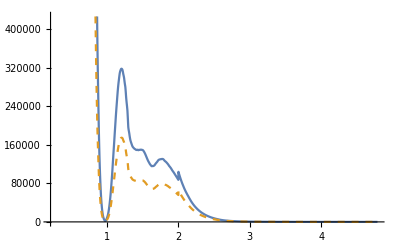

```mathematica
Plot[{norm[mS,0.0001,mK],Nnorm[mS,0.0001,mK]},{mS,2mμ/.masses,mB-mK/.masses},PlotStyle->{Plain,Dashed}]
```

```mathematica
ΔN[mS_]:=(Nnorm[mS,0.0001,mK]-norm[mS,0.0001,mK])/Nnorm[mS,0.0001,mK]
```

```mathematica
ΔN[0.5]
ΔN[1]
ΔN[1.1]
ΔN[1.2]
ΔN[1.3]
ΔN[1.4]
ΔN[1.5]
ΔN[1.6]
ΔN[1.7]
ΔN[1.8]
ΔN[1.9]
ΔN[2.01]
ΔN[2.5]
ΔN[3]
ΔN[3.5]
ΔN[4]
```

4.34046×10^-16+0. ⅈ

4.56939×10^-16+0. ⅈ

8.39943×10^-16+0. ⅈ

6.67476×10^-16+0. ⅈ

5.32524×10^-16+0. ⅈ

6.82045×10^-16+0. ⅈ

3.3813×10^-16+0. ⅈ

6.1636×10^-16+0. ⅈ

1.95985×10^-16+0. ⅈ

5.55707×10^-16+0. ⅈ

0.+0. ⅈ

3.42137×10^-16+0. ⅈ

3.36772×10^-16+0. ⅈ

1.21184×10^-16+0. ⅈ

1.72677×10^-16+0. ⅈ

7.05608×10^-16+0. ⅈ

#### Reasoning

```mathematica
Timing[norm[2.5,0.0001,mK]]
Timing[Nnorm[2.5,0.0001,mK]]
```

{0.005112,5401.25+0. ⅈ}

{0.107114,5401.25}

```mathematica
normρInt=Integrate[ρ^2Exp[-a ρ],{ρ,0,Infinity}]//Normal
```

```mathematica
normθ0intd=2(γB+γβB ES/pS Cos[θ0])/Sin[θ0]^2((cτS pS Sin[θ0])/mS)^3
```

```mathematica
mS^2/.Solve[(pS+βB ES Cos[θ0]//.Eptransl)==0,{mS}]//Simplify//PowerExpand//Simplify//DeleteDuplicates
```

{-1/(βB^2 cos^2(θ0)-1)(βB^2 cos^2(θ0) (mB^2-mKX^2)+√2 mB √(βB^2 mB^2+βB^2 cos(2 θ0) (mB^2-mKX^2)-(βB^2-2) mKX^2)+mB^2+mKX^2),-1/(βB^2 cos^2(θ0)-1)(βB^2 cos^2(θ0) (mB^2-mKX^2)-√2 mB √(βB^2 mB^2+βB^2 cos(2 θ0) (mB^2-mKX^2)-(βB^2-2) mKX^2)+mB^2+mKX^2)}

```mathematica
Sqrt[(mS^2/.Solve[(pS+βB ES Cos[θ0]//.Eptransl)==0,{mS}]//Simplify//PowerExpand//Simplify//DeleteDuplicates)/.masses/.{βB:>γβB/γB}/.BIIparams/.θ0:>π][[2]]
```

1.03834 √(0.0724852 (27.8678-mKX^2)-7.46563 √(0.0724852 (27.8678-mKX^2)+1.92751 mKX^2+2.02001)+mKX^2+27.8678)

```mathematica
Sin[θ0]^2/.Solve[(pS+βB ES Cos[θ0])==0,{θ0}]/.C[1]:>0//FullSimplify//DeleteDuplicates//ExpandNumerator
Cos[θ0]/.Solve[(pS+βB ES Cos[θ0])==0,{θ0}]/.C[1]:>0//FullSimplify//DeleteDuplicates//Expand
```

{1-pS^2/(βB^2 ES^2)}

{-pS/(βB ES)}

```mathematica
Integrate[Sin[x],{x,0,b}]
Integrate[Sin[x]Cos[x],{x,0,b}]
Integrate[Sin[x],{x,b,π}]
Integrate[Sin[x]Cos[x],{x,b,π}]
```

1-cos(b)

(sin^2(b))/2

cos(b)+1

-1/2 sin^2(b)

```mathematica
Nnorm[mSp_,α_,mKXp_]:= NIntegrate[2 Abs[γB+γβB ES/pS Cos[θ0]]/Sin[θ0]^2((cτS[mSp,α] pS Sin[θ0])/mSp)^3//.Eptransl/.mS:>mSp/.mKX:>mKXp/.BIIparams/.masses,{θ0,0,π}]
```

### Angles

```mathematica
dθoversinsqrθbydθ0[θ0_,mSp_,mKXp_]=Abs[(γB+γβB ES/pS Cos[θ0])/Sin[θ0]^2//.Eptransl/.mKX:>mKXp/.mS:>mSp]
```

Abs[csc^2(θ0) (γB+(γβB cos(θ0) (mB^2-mKXp^2+mSp^2))/(2 mB √(((mB^2-mKXp^2+mSp^2)^2)/(4 mB^2)-mSp^2)))]

```mathematica
Cotθ[θ0_,mS_]=(γβB ES+γB pS Cos[θ0])/(pS Sin[θ0])//.Eptransl//Simplify
```

γB cot(θ0)+(γβB csc(θ0) (mB^2-mKX^2+mS^2))/(mB √(((mKX^2-mS^2)^2)/mB^2+mB^2-2 (mKX^2+mS^2)))

```mathematica
Sinθ[θ0_,mS_]=(pS Sin[θ0])/Sqrt[pS^2Sin[θ0]^2+(γβB ES+γB Cos[θ0]pS)^2]//.Eptransl//Simplify
```

(sin(θ0) √(((mB^2-mKX^2+mS^2)^2)/(4 mB^2)-mS^2))/(√((γB cos(θ0) √(((mB^2-mKX^2+mS^2)^2)/(4 mB^2)-mS^2)+(γβB (mB^2-mKX^2+mS^2))/(2 mB))^2+sin^2(θ0) (((mB^2-mKX^2+mS^2)^2)/(4 mB^2)-mS^2)))

```mathematica
θcutoff[mSp_,mKXp_]:=θ/.Solve[(pS^2 γB^2-ES^2 γβB^2+pS^2 Cot[θ]^2//.Eptransl/.BIIparams/.mKX:>mKXp/.masses/.mS:>mSp)==0,{θ}]
θmax[mS_,mKXp_]:=Quiet[Max[Min[Select[θcutoff[mS,mKXp],(Head[#]===Real&&#>0&&#<π/2)&],150°](*,17°*)]]
```

```mathematica
θ0ofθ=θ0/.Solve[Cot[θ]==(γβB ES+γB pS Cos[θ0])/(pS Sin[θ0]),{θ0}]//Simplify//PowerExpand//Simplify//#/.{ArcTan[a_,b_]:>ArcTan[a*(γB^2pS+pS Cot[θ]^2),b*(γB^2pS+pS Cot[θ]^2)]}&//Simplify//#/.C[1]:>0&
```

{tan^-1(γB γβB (-ES)-cot(θ) √(-γβB^2 ES^2+γB^2 pS^2+pS^2 cot^2(θ)),γβB ES cot(θ)-γB √(-γβB^2 ES^2+γB^2 pS^2+pS^2 cot^2(θ))),tan^-1(cot(θ) √(-γβB^2 ES^2+γB^2 pS^2+pS^2 cot^2(θ))-γB γβB ES,γB √(-γβB^2 ES^2+γB^2 pS^2+pS^2 cot^2(θ))+γβB ES cot(θ))}

```mathematica
Nθ0ofθ[θp_,mSp_,mKXp_]:=θ0ofθ//.Eptransl/.mKX:>mKXp//.masses/.BIIparams/.{mS:>mSp,θ:>θp}
```

```mathematica
Timing[Nθ0ofθ[0.6,1.7,mK]]
```

{0.003024,{-2.71741,0.812625}}

```mathematica
Manipulate[Plot[{Nθ0ofθ[θ °,mS][[1]]/°,Nθ0ofθ[θ °,mS][[2]]/°},{θ,0,180},AxesLabel->{"θ [°]","θ_0 [°]"},PlotLabel->StringForm["m_S=``GeV",mS],GridLines->{{17,θmax[mS,mK]/°,150},{}},PlotRange->{0,180},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,14]],{mS,2mμ/.masses,mB-mK/.masses}]
```

```mathematica
θ0min[mS_,mKXp_]:=(tmin=Nθ0ofθ[17°,mS,mKXp][[2]];If[Head[tmin]===Complex,0,tmin])
```

```mathematica
θ0max[mS_,mKXp_]:=(tmax=(If[θmax[mS,mKXp]==150°,Nθ0ofθ[150°,mS,mKXp][[2]],Nθ0ofθ[17°,mS,mKXp][[1]]]);If[Head[tmax]===Complex,0,tmax])
```

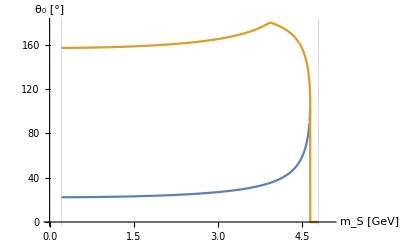

```mathematica
Plot[{θ0min[mS,mK]/°,θ0max[mS,mK]/°},{mS,2mμ/.masses,mB-mK/.masses},AxesLabel->{"m_S [GeV]","θ_0 [°]"},PlotRange->{{0,5},{0,180}},GridLines->{{2mμ/.masses,mB-mK/.masses},{}},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

### Integral proper

```mathematica
Nθ0intdECL[mSp_?NumericQ,α_?NumericQ,θ0_?NumericQ,mKXp_]:=dθoversinsqrθbydθ0[θ0,mSp,mKXp]Block[{a=mS/(cτS[mS,α] pS Sin[θ0])//.Eptransl/.mS:>mSp/.mKX:>mKXp/.ECLparams/.BIIparams/.masses,b=Cotθ[θ0,mS]/.ECLparams/.mKX:>mKXp/.BIIparams/.masses/.mS:>mSp},NIntegrate[ρ^2Exp[-a ρ]HeavisideTheta[ρ b-zmin] HeavisideTheta[-ρ b + zmax]/.ECLparams,{ρ,dres Sinθ[θ0,mSp]/.mKX:>mKXp/.BIIparams/.masses,ρmax/.ECLparams}]]/.BIIparams/.masses;
```

```mathematica
NintECL[mS_,α_,mKXp_]:=Block[{θ0min=θ0min[mS,mKXp],θ0max=θ0max[mS,mKXp]},NIntegrate[Nθ0intdECL[mS,α,θ0,mKXp],{θ0,θ0min,θ0max},AccuracyGoal->3]]/norm[mS,α,mKXp]
```

```mathematica
Nθ0intdCDC[mSp_?NumericQ,α_?NumericQ,θ0_?NumericQ,mKXp_]:=dθoversinsqrθbydθ0[θ0,mSp,mKXp]Block[{a=mS/(cτS[mS,α] pS Sin[θ0])//.Eptransl/.mS:>mSp/.mKX:>mKXp/.CDCparams/.BIIparams/.masses,b=Cotθ[θ0,mS]/.CDCparams/.mKX:>mKXp/.BIIparams/.masses/.mS:>mSp},NIntegrate[ρ^2Exp[-a ρ]HeavisideTheta[ρ b-zmin] HeavisideTheta[-ρ b + zmax]/.CDCparams,{ρ,dres Sinθ[θ0,mSp]/.mKX:>mKXp/.BIIparams/.masses,ρmax/.CDCparams}]]/.BIIparams/.masses;
```

```mathematica
NintCDC[mS_,α_,mKXp_]:=Block[{θ0min=θ0min[mS,mKXp],θ0max=θ0max[mS,mKXp]},NIntegrate[Nθ0intdCDC[mS,α,θ0,mKXp],{θ0,θ0min,θ0max},AccuracyGoal->3]]/norm[mS,α,mKXp]
```

```mathematica
Timing[NintECL[0.9,0.0001,mK]]
Timing[NintCDC[0.9,0.0001,mK]]
Timing[NintECL[3,0.0001,mK]]
Timing[NintCDC[3,0.0001,mK]]
```

{5.52368,0.888947+0. ⅈ}

{13.7724,0.810277+0. ⅈ}

{0.377605,0.909918+0. ⅈ}

{0.349892,0.909918+0. ⅈ}

## Branching ratios

### B^+->K^+S pseudoscalar

```mathematica
ΓBtoKPϕ[mϕ_,α_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 fzero[mϕ^2]^2 (MB+MS)^2 √((mB^2-(mK-mϕ)^2)  (mB^2-(mK+mϕ)^2))((2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2/ (MW^2-MT^2)^6))((mB^2-mK^2)^2)/(4194304 π^5 mB^3 MW^6 SW^6 (MB-MS)^2)HeavisideTheta[mB-(mK+mϕ)]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKP[mS_,α_]:=ΓBtoKPϕ[mS,α]/ΓtotalB
```

### B^+->K^(*+)S scalar

```mathematica
ΓBtoKstarSϕGen[mϕ_,α_,mKscalar_,F0_,a_,b_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 fplus[mϕ^2,F0,a,b]^2 (MB+MS)^2 √((mB^2-(mKscalar-mϕ)^2)  (mB^2-(mKscalar+mϕ)^2))1/((MW^2-MT^2)^6)(2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2)((mB^2-mKscalar^2-mϕ^2)^2)/(4194304 π^5 mB^3 MW^6 SW^6 (MB+MS)^2)HeavisideTheta[mB-(mKscalar+mϕ)]
```

```mathematica
BrBtoSKS700[mS_,α_]:=ΓBtoKstarSϕGen[mS,α,mKstarS700,F0BS700,aS700,bS700]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKS1430[mS_,α_]:=ΓBtoKstarSϕGen[mS,α,mKstarS1430,F0BS1430,aS1430,bS1430]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms
```

### B^+->K^(*+)S vector

```mathematica
ΓBtoKstarVϕGen[mϕ_,α_,mKstar_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 Azero[mϕ^2,mKstar]^2 (MB+MS)^2 √((mB^2-(mKstar-mϕ)^2)  (mB^2-(mKstar+mϕ)^2))((2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2/ (MW^2-MT^2)^6))((mB^2-(mKstar-mϕ)^2)  (mB^2-(mKstar+mϕ)^2))/(4194304 π^5 mB^3 MW^6 SW^6 (MB+MS)^2)HeavisideTheta[mB-(mKstar+mϕ)]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKV892[mS_,α_]:=ΓBtoKstarVϕGen[mS,α,mKstarV892]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKV1410[mS_,α_]:=ΓBtoKstarVϕGen[mS,α,mKstarV1410]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKV1680[mS_,α_]:=ΓBtoKstarVϕGen[mS,α,mKstarV1680]/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms
```

### B^+->K^(*+)S axialvector

```mathematica
ΓBtoKAVϕGen[mϕ_,α_,mKstar_]:=Sin[α]^2(EL^6 MT^4 Vtb^2 (Conjugate[Vts])^2 V0[mϕ^2]^2 (MB+MS)^2 √((mB^2-(mKstar-mϕ)^2)  (mB^2-(mKstar+mϕ)^2))1/((MW^2-MT^2)^6)(2 MT^2 mϕ^2 (MT^2-2 MW^2) (Log[MT^2]-Log[MW^2])+6 (MT^2-MW^2)^3-mϕ^2 (MT^4-4 MT^2 MW^2+3 MW^4))^2)((mB^2-(mKstar-mϕ)^2)  (mB^2-(mKstar+mϕ)^2))/(4194304 π^5 mB^3 MW^6 SW^6 (MB-MS)^2)HeavisideTheta[mB-(mKstar+mϕ)]
```

```mathematica
BrBtoSKA1270[mS_,α_]:=ΓBtoKstarVϕGen[mS,α,mKAV1270]/.V0-> V0BK1270/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrBtoSKA1400[mS_,α_]:=ΓBtoKstarVϕGen[mS,α,mKAV1400]/.V0-> V0BK1400/ΓtotalB/.formFactors/.values/.masses/.couplings/.ckms
```

### Plot

```mathematica
BrsPlot[α_]:=Plot[{BrBtoSKP[mS,α],BrBtoSKS700[mS,α],BrBtoSKS1430[mS,α],BrBtoSKV892[mS,α],BrBtoSKV1410[mS,α],BrBtoSKV1680[mS,α],BrBtoSKA1270[mS,α],BrBtoSKA1400[mS,α]},{mS,0,mB/.masses},PlotLegends->{P490,S700,S1430,V892,V1410,V1680,A1270,A1400}]
```

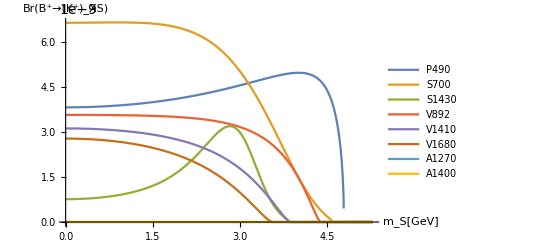

```mathematica
Show[BrsPlot[0.0001],AxesLabel->{"m_S[GeV]","Br(B^+→(K^+)_XS)"},AxesStyle->Directive[Black, 14],LabelStyle->Directive[Black,16]]
```

### S->ff branching ratios

```mathematica
BrSμμ[mS_,α_]:=Γϕtoμμ[mS,α]/ΓϕBRDM[mS,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrSττ[mS_,α_]:=Γϕtoττ[mS,α]/ΓϕBRDM[mS,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrSππ[mS_,α_]:=Γϕπ[mS,α]/ΓϕBRDM[mS,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

```mathematica
BrSKK[mS_,α_]:=ΓϕK[mS,α]/ΓϕBRDM[mS,α,0]/.formFactors/.values/.masses/.couplings/.ckms
```

## Decay Numbers

### Auxiliary

```mathematica
BtoSKXinECL[mS_,α_]:=BrBtoSKP[mS,α] NintECL[mS,α,mK]+BrBtoSKS700[mS,α] NintECL[mS,α,mKstarS700]+BrBtoSKS1430[mS,α] NintECL[mS,α,mKstarS1430]+BrBtoSKV892[mS,α] NintECL[mS,α,mKstarV892]+BrBtoSKV1410[mS,α] NintECL[mS,α,mKstarV1410]+BrBtoSKV1680[mS,α] NintECL[mS,α,mKstarV1680]+BrBtoSKA1270[mS,α] NintECL[mS,α,mKAV1270]+BrBtoSKA1400[mS,α] NintECL[mS,α,mKAV1400]
```

```mathematica
BtoSKXinCDC[mS_,α_]:=BrBtoSKP[mS,α] NintCDC[mS,α,mK]+BrBtoSKS700[mS,α] NintCDC[mS,α,mKstarS700]+BrBtoSKS1430[mS,α] NintCDC[mS,α,mKstarS1430]+BrBtoSKV892[mS,α] NintCDC[mS,α,mKstarV892]+BrBtoSKV1410[mS,α] NintCDC[mS,α,mKstarV1410]+BrBtoSKV1680[mS,α] NintCDC[mS,α,mKstarV1680]+BrBtoSKA1270[mS,α] NintCDC[mS,α,mKAV1270]+BrBtoSKA1400[mS,α] NintCDC[mS,α,mKAV1400]
```

### Definitions

```mathematica
NμμECL[mS_,α_]:=1.93NBBBelleII  BtoSKXinECL[mS,α]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NμμCDC[mS_,α_]:=1.93NBBBelleII  BtoSKXinCDC[mS,α]BrSμμ[mS,α]/.BIIparams
```

```mathematica
NππECL[mS_,α_]:=1.93NBBBelleII BtoSKXinECL[mS,α]BrSππ[mS,α]/.BIIparams
```

```mathematica
NππCDC[mS_,α_]:=1.93NBBBelleII BtoSKXinCDC[mS,α]BrSππ[mS,α]/.BIIparams
```

```mathematica
NKKECL[mS_,α_]:=1.93NBBBelleII BtoSKXinECL[mS,α]BrSKK[mS,α]/.BIIparams
```

```mathematica
NKKCDC[mS_,α_]:=1.93NBBBelleII BtoSKXinCDC[mS,α]BrSKK[mS,α]/.BIIparams
```

```mathematica
NττECL[mS_,α_]:=1.93NBBBelleII BtoSKXinECL[mS,α]BrSττ[mS,α]/.BIIparams
```

```mathematica
NττCDC[mS_,α_]:=1.93NBBBelleII BtoSKXinCDC[mS,α]BrSττ[mS,α]/.BIIparams
```

### Checks

```mathematica
NμμECL[3,0.0001]//Timing
NμμCDC[3,0.0001]//Timing
NππECL[1,0.0001]//Timing
NππCDC[1,0.0001]//Timing
NKKECL[1,0.0001]//Timing
NKKCDC[1,0.0001]//Timing
NττECL[4,0.0001]//Timing
NττCDC[4,0.0001]//Timing
```

{13.3999,147.619+0. ⅈ}

{13.469,147.619+0. ⅈ}

{14.6874,1256.72+0. ⅈ}

{19.8413,1256.34+0. ⅈ}

{15.0819,548.09+0. ⅈ}

{19.9483,547.925+0. ⅈ}

{14.2332,268.707+0. ⅈ}

{13.4025,268.707+0. ⅈ}

## Plots

### Auxiliary

```mathematica
mSlist=Range[2mμ/.masses,mB-mK/.masses,0.05]
mSlistπK=Range[2mπ/.masses,2,0.05]
mSlistτ=Range[2mτ/.masses,mB-mK/.masses,0.05]
```

{0.212,0.262,0.312,0.362,0.412,0.462,0.512,0.562,0.612,0.662,0.712,0.762,0.812,0.862,0.912,0.962,1.012,1.062,1.112,1.162,1.212,1.262,1.312,1.362,1.412,1.462,1.512,1.562,1.612,1.662,1.712,1.762,1.812,1.862,1.912,1.962,2.012,2.062,2.112,2.162,2.212,2.262,2.312,2.362,2.412,2.462,2.512,2.562,2.612,2.662,2.712,2.762,2.812,2.862,2.912,2.962,3.012,3.062,3.112,3.162,3.212,3.262,3.312,3.362,3.412,3.462,3.512,3.562,3.612,3.662,3.712,3.762,3.812,3.862,3.912,3.962,4.012,4.062,4.112,4.162,4.212,4.262,4.312,4.362,4.412,4.462,4.512,4.562,4.612,4.662,4.712,4.762}

{0.28,0.33,0.38,0.43,0.48,0.53,0.58,0.63,0.68,0.73,0.78,0.83,0.88,0.93,0.98,1.03,1.08,1.13,1.18,1.23,1.28,1.33,1.38,1.43,1.48,1.53,1.58,1.63,1.68,1.73,1.78,1.83,1.88,1.93,1.98}

{3.554,3.604,3.654,3.704,3.754,3.804,3.854,3.904,3.954,4.004,4.054,4.104,4.154,4.204,4.254,4.304,4.354,4.404,4.454,4.504,4.554,4.604,4.654,4.704,4.754}

```mathematica
myColours={ColorData[3,"ColorList"][[6]],Darker[ColorData[3,"ColorList"][[6]]],ColorData[3,"ColorList"][[2]],Darker[ColorData[3,"ColorList"][[2]]],ColorData[3,"ColorList"][[4]],Darker[ColorData[3,"ColorList"][[4]]]}
```

{RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.005228758169934641, 0.33986928104575165, 0.6196078431372549],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.6640522875816994, 0.24052287581699347, 0.018300653594771243],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.3607843137254902, 0.4758169934640523, 0.018300653594771243]}

### geoInt

```mathematica
intECLpoints=ParallelTable[NintECL[mS,0.0001,mK],{mS,mSlist}]//Quiet
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.50317}. NIntegrate obtained 441411. and 1.66219 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720302}. NIntegrate obtained 3.43582×10^6 and 118.613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.50403}. NIntegrate obtained 174949. and 0.394973 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720458}. NIntegrate obtained 3.42668×10^6 and 120.349 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720648}. NIntegrate obtained 3.30051×10^6 and 73.9019 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.733133}. NIntegrate obtained 87131. and 0.107787 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 224 125 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 146).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{4.64285×10^-20,6.31467×10^-9,0.0000203737,0.000216588,0.00112451,0.0039997,0.0109863,0.0270602,0.0542177,0.100601,0.178209,0.306829,0.503383,0.751662,0.90912,0.923369,0.923212,0.907025,0.853362,0.806982,0.793114,0.81099,0.851833,0.865944,0.868501,0.867652,0.867947,0.875428,0.881889,0.881721,0.875827,0.872895,0.874218,0.87772,0.882885,0.888348,0.886229,0.897505,0.905522,0.911392,0.915448,0.917762,0.918922,0.919354,0.919346,0.919077,0.918651,0.918123,0.917515,0.916835,0.916082,0.91525,0.91433,0.913314,0.912191,0.910949,0.909575,0.908055,0.906371,0.904504,0.902433,0.900133,0.897576,0.894729,0.891555,0.888012,0.884049,0.879609,0.874625,0.869017,0.862694,0.855543,0.84743,0.838199,0.82769,0.815715,0.802822,0.78778,0.768873,0.750951,0.730859,0.705183,0.672734,0.631895,0.582219,0.527331,0.449525,0.33518,0.155606,0.,0.,0.}

```mathematica
intCDCpoints=ParallelTable[NintCDC[mS,0.0001,mK],{mS,mSlist}]//Quiet
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.802938}. NIntegrate obtained 1.30477×10^6 and 65.0753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.3469}. NIntegrate obtained 285721. and 3.78567 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.803099}. NIntegrate obtained 1.30229×10^6 and 32.1242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.812372}. NIntegrate obtained 136142. and 0.923875 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.803293}. NIntegrate obtained 1.26805×10^6 and 54.4955 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.813007}. NIntegrate obtained 32545.1 and 0.0748512 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.37479}. NIntegrate obtained 65153.6 and 0.272255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.3764}. NIntegrate obtained 65681.9 and 0.34249 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.833288}. NIntegrate obtained 65418.1 and 0.288129 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.857908}. NIntegrate obtained 51032.9 and 0.145732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.864479}. NIntegrate obtained 41687.7 and 0.0854649 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.866505}. NIntegrate obtained 34010.5 and 0.054675 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 150 65 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 113).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{1.76315×10^-20,2.39985×10^-9,7.82755×10^-6,0.0000843993,0.000446954,0.00163072,0.00462145,0.011858,0.0248375,0.0486464,0.0923113,0.174454,0.325835,0.584931,0.862785,0.923298,0.921153,0.856736,0.738709,0.662556,0.642197,0.668856,0.736371,0.762814,0.767937,0.766406,0.767128,0.782324,0.796122,0.795938,0.783689,0.7779,0.780821,0.788297,0.79959,0.812087,0.807579,0.834796,0.856827,0.875433,0.890668,0.901464,0.908729,0.913322,0.915992,0.917342,0.91783,0.917784,0.917396,0.916795,0.916069,0.915245,0.914329,0.913313,0.91219,0.910949,0.909575,0.908055,0.906371,0.904504,0.902433,0.900133,0.897576,0.894729,0.891555,0.888012,0.884049,0.879609,0.874625,0.869017,0.862694,0.855543,0.84743,0.838199,0.82769,0.815715,0.802822,0.78778,0.768873,0.750951,0.730859,0.705183,0.672734,0.631895,0.582219,0.527331,0.449525,0.33518,0.155606,0.,0.,0.}

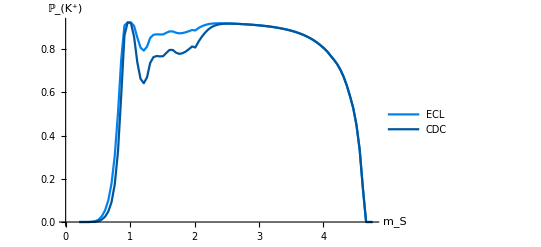

```mathematica
Show[ListPlot[Thread[{mSlist,intECLpoints}], Joined->True,PlotStyle->myColours[[1]],PlotLegends->{ECL}],ListPlot[Thread[{mSlist,intCDCpoints}], Joined->True,PlotStyle->myColours[[2]],PlotLegends->{CDC}],AxesLabel->{Subscript[m, S],Subscript[ℙ, SuperPlus[K]]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

### NXX

```mathematica
NmmECLpoints=ParallelTable[NμμECL[mS,0.0001],{mS,mSlist}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.50317}. NIntegrate obtained 441411. and 1.66219 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720302}. NIntegrate obtained 3.43582×10^6 and 118.613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.50329}. NIntegrate obtained 433779. and 2.4671 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720307}. NIntegrate obtained 3.43582×10^6 and 119.5 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.50418}. NIntegrate obtained 385640. and 1.94392 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720345}. NIntegrate obtained 3.43587×10^6 and 110.911 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.812} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.262} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.862} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.062} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.756015}. NIntegrate obtained 64324.5 and 0.0726249 for the integral and error estimates.

InterpolatingFunction::dmval: Input value {2.612} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.662} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.162} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 224 125 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 146).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 224 125 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 146).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.762} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 224 125 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 146).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.262} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
NmmCDCpoints=ParallelTable[NμμCDC[mS,0.0001],{mS,mSlist}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.802938}. NIntegrate obtained 1.30477×10^6 and 65.0753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.3469}. NIntegrate obtained 285721. and 3.78567 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.802944}. NIntegrate obtained 1.30477×10^6 and 65.8378 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.802982}. NIntegrate obtained 1.30478×10^6 and 60.5617 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.34702}. NIntegrate obtained 281875. and 3.87044 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.812474}. NIntegrate obtained 257138. and 4.04804 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.812} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.262} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.862} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.37479}. NIntegrate obtained 65153.6 and 0.272255 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.826652}. NIntegrate obtained 63409.1 and 0.360037 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.83347}. NIntegrate obtained 52711.5 and 0.230757 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.857908}. NIntegrate obtained 51032.9 and 0.145732 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.858723}. NIntegrate obtained 49209.9 and 0.125344 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.869451}. NIntegrate obtained 38119.1 and 0.103501 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.012} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.062} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.612} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.662} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.162} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.212} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 150 65 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 113).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 150 65 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 113).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.712} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.762} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 150 65 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 113).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.262} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.312} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

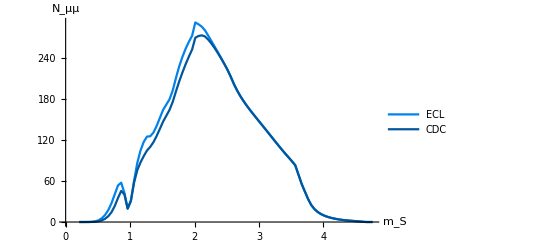

```mathematica
Show[ListPlot[Thread[{mSlist,NmmECLpoints}], Joined->True,PlotStyle->myColours[[1]],PlotLegends->{ECL}],ListPlot[Thread[{mSlist,NmmCDCpoints}], Joined->True,PlotStyle->myColours[[2]],PlotLegends->{CDC}],AxesLabel->{Subscript[m, S],Subscript[N, μμ]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

```mathematica
NppECLpoints=ParallelTable[NππECL[mS,0.0001],{mS,mSlistπK}];
```

NIntegrate::inumr: The integrand (1.29419×10^-38 1.04 sin(θ0))/(«1»)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 3.14159).

NIntegrate::inumr: The integrand (1.25959×10^-38 1.04 sin(θ0))/(«1»)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 3.14159).

NIntegrate::inumr: The integrand (1.05518×10^-38 1.04 sin(θ0))/(«1»)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 3.14159).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.722246}. NIntegrate obtained 1.96527×10^6 and 39.678 for the integral and error estimates.

InterpolatingFunction::dmval: Input value {0.28} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.722287}. NIntegrate obtained 1.95531×10^6 and 34.1351 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720725}. NIntegrate obtained 3.24996×10^6 and 81.6186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.722579}. NIntegrate obtained 1.8893×10^6 and 56.824 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720738}. NIntegrate obtained 3.24831×10^6 and 83.5689 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720829}. NIntegrate obtained 3.23712×10^6 and 107.021 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.58} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.38} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

InterpolatingFunction::dmval: Input value {0.68} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.729847}. NIntegrate obtained 110557. and 0.171589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.730658}. NIntegrate obtained 91005.8 and 0.1181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.730077}. NIntegrate obtained 104393. and 0.172713 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.88} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.734269}. NIntegrate obtained 134709. and 0.302699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.734463}. NIntegrate obtained 131210. and 0.274194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.735849}. NIntegrate obtained 109895. and 0.164031 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.756036}. NIntegrate obtained 68093.3 and 0.0824579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.75721}. NIntegrate obtained 62910.5 and 0.0702399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.765308}. NIntegrate obtained 62782.5 and 0.0848606 for the integral and error estimates.

```mathematica
NppCDCpoints=ParallelTable[NππCDC[mS,0.0001],{mS,mSlistπK}];
```

NIntegrate::inumr: The integrand (1.29419×10^-38 1.04 sin(θ0))/(«1»)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 3.14159).

NIntegrate::inumr: The integrand (1.25959×10^-38 1.04 sin(θ0))/(«1»)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 3.14159).

NIntegrate::inumr: The integrand (1.05518×10^-38 1.04 sin(θ0))/(«1»)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 3.14159).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.28} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.832487}. NIntegrate obtained 874104. and 28.6882 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.803371}. NIntegrate obtained 1.25409×10^6 and 47.0136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.804969}. NIntegrate obtained 870888. and 30.2961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.803384}. NIntegrate obtained 1.25363×10^6 and 46.4909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.803478}. NIntegrate obtained 1.25058×10^6 and 35.7906 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.805267}. NIntegrate obtained 849482. and 21.5949 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.58} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.38} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.68} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.812596}. NIntegrate obtained 92583.9 and 0.439509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.3482}. NIntegrate obtained 90598.7 and 0.302648 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.35382}. NIntegrate obtained 78310.3 and 0.30988 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.88} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.849338}. NIntegrate obtained 109536. and 0.349041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.36392}. NIntegrate obtained 107137. and 0.551843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.82334}. NIntegrate obtained 92169.2 and 0.695394 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.832518}. NIntegrate obtained 65970.4 and 0.239206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.37749}. NIntegrate obtained 64169.4 and 0.150635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.835358}. NIntegrate obtained 53111.7 and 0.22222 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.39779}. NIntegrate obtained 61818.7 and 0.177059 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.845875}. NIntegrate obtained 59900.8 and 0.311665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.854662}. NIntegrate obtained 48148.1 and 0.134055 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

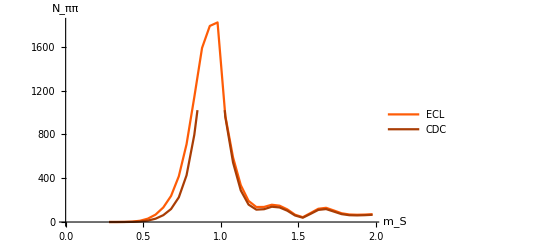

```mathematica
Show[ListPlot[Thread[{mSlistπK,NppECLpoints}], Joined->True,PlotStyle->myColours[[3]],PlotLegends->{ECL}],ListPlot[Thread[{mSlistπK,NppCDCpoints}], Joined->True,PlotStyle->myColours[[4]],PlotLegends->{CDC}],AxesLabel->{Subscript[m, S],Subscript[N, ππ]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16]]
```

```mathematica
NkkECLpoints=ParallelTable[NKKECL[mS,0.0001],{mS,mSlistπK}];
```

NIntegrate::inumr: The integrand (1.29419×10^-38 1.04 sin(θ0))/(«1»)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 3.14159).

NIntegrate::inumr: The integrand (1.25959×10^-38 1.04 sin(θ0))/(«1»)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 3.14159).

NIntegrate::inumr: The integrand (1.05518×10^-38 1.04 sin(θ0))/(«1»)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 3.14159).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.722246}. NIntegrate obtained 1.96527×10^6 and 39.678 for the integral and error estimates.

InterpolatingFunction::dmval: Input value {0.28} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.722287}. NIntegrate obtained 1.95531×10^6 and 34.1351 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720725}. NIntegrate obtained 3.24996×10^6 and 81.6186 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.722579}. NIntegrate obtained 1.8893×10^6 and 56.824 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720738}. NIntegrate obtained 3.24831×10^6 and 83.5689 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720829}. NIntegrate obtained 3.23712×10^6 and 107.021 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.58} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.729847}. NIntegrate obtained 110557. and 0.171589 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.730658}. NIntegrate obtained 91005.8 and 0.1181 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.730077}. NIntegrate obtained 104393. and 0.172713 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.88} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.734269}. NIntegrate obtained 134709. and 0.302699 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.734463}. NIntegrate obtained 131210. and 0.274194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.735849}. NIntegrate obtained 109895. and 0.164031 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.756036}. NIntegrate obtained 68093.3 and 0.0824579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.75721}. NIntegrate obtained 62910.5 and 0.0702399 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.765308}. NIntegrate obtained 62782.5 and 0.0848606 for the integral and error estimates.

```mathematica
NkkCDCpoints=ParallelTable[NKKCDC[mS,0.0001],{mS,mSlistπK}];
```

NIntegrate::inumr: The integrand (1.29419×10^-38 1.04 sin(θ0))/(«1»)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 3.14159).

NIntegrate::inumr: The integrand (1.25959×10^-38 1.04 sin(θ0))/(«1»)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 3.14159).

NIntegrate::inumr: The integrand (1.05518×10^-38 1.04 sin(θ0))/(«1»)^3 has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 3.14159).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.28} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.832487}. NIntegrate obtained 874104. and 28.6882 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.803371}. NIntegrate obtained 1.25409×10^6 and 47.0136 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.804969}. NIntegrate obtained 870888. and 30.2961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.803384}. NIntegrate obtained 1.25363×10^6 and 46.4909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.803478}. NIntegrate obtained 1.25058×10^6 and 35.7906 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.805267}. NIntegrate obtained 849482. and 21.5949 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.58} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.812596}. NIntegrate obtained 92583.9 and 0.439509 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.3482}. NIntegrate obtained 90598.7 and 0.302648 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.35382}. NIntegrate obtained 78310.3 and 0.30988 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.88} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.849338}. NIntegrate obtained 109536. and 0.349041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.36392}. NIntegrate obtained 107137. and 0.551843 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.82334}. NIntegrate obtained 92169.2 and 0.695394 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.832518}. NIntegrate obtained 65970.4 and 0.239206 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.37749}. NIntegrate obtained 64169.4 and 0.150635 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.835358}. NIntegrate obtained 53111.7 and 0.22222 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {2.39779}. NIntegrate obtained 61818.7 and 0.177059 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.845875}. NIntegrate obtained 59900.8 and 0.311665 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.854662}. NIntegrate obtained 48148.1 and 0.134055 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

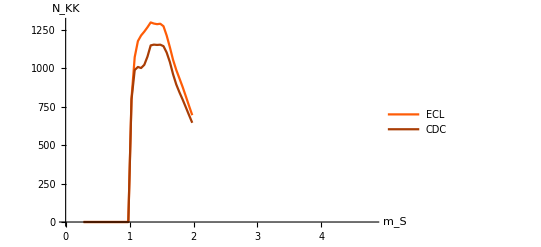

```mathematica
Show[ListPlot[Thread[{mSlistπK,NkkECLpoints}], Joined->True,PlotStyle->myColours[[3]],PlotLegends->{ECL}],ListPlot[Thread[{mSlistπK,NkkCDCpoints}], Joined->True,PlotStyle->myColours[[4]],PlotLegends->{CDC}],AxesLabel->{Subscript[m, S],Subscript[N, KK]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16],PlotRange->{{0,4.8},Automatic}]
```

```mathematica
NttECLpoints=ParallelTable[NττECL[mS,0.0001],{mS,mSlistτ}];
```

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 224 125 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 146).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.804} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.554} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.854} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.604} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 224 125 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 146).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.054} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 224 125 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 146).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.204} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.254} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 224 125 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 146).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.404} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 224 125 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 146).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.454} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.604} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.654} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
NttCDCpoints=ParallelTable[NττCDC[mS,0.0001],{mS,mSlistτ}];
```

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 150 65 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 113).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 150 65 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 113).

InterpolatingFunction::dmval: Input value {3.804} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 150 65 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 113).

InterpolatingFunction::dmval: Input value {3.804} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.554} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.854} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.604} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 150 65 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 113).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.004} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.054} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 150 65 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 113).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.204} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.254} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 150 65 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 113).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.404} lies outside the range of data in the interpolating function. Extrapolation will be used.

NIntegrate::inumr: The integrand ⅇ^(-a ρ) ρ^2 150 65 has evaluated to non-numerical values for all sampling points in the region with boundaries (0. | 113).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.454} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.604} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.654} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

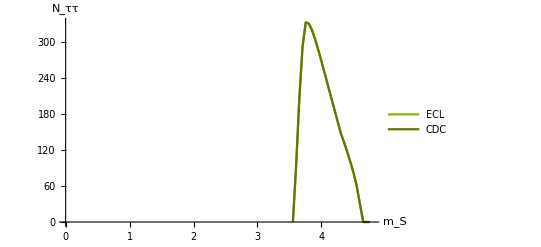

```mathematica
Show[ListPlot[Thread[{mSlistτ,NttECLpoints}], Joined->True,PlotStyle->myColours[[5]],PlotLegends->{ECL}],ListPlot[Thread[{mSlistτ,NttCDCpoints}], Joined->True,PlotStyle->myColours[[6]],PlotLegends->{CDC}],AxesLabel->{Subscript[m, S],Subscript[N, ττ]},AxesStyle->Directive[Black,14],LabelStyle->Directive[Black,16],PlotRange->{{0,4.8},Automatic},AxesOrigin->{0,0}]
```

### Contour

```mathematica
CPμμECL=ContourPlot[NμμECL[mS,α],{mS,2mμ/.masses,mB-mK/.masses},{α,10^-6,0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","α"},ContourShading->None,ContourStyle->{ColorData[3,"ColorList"][[6]]},Contours->{3}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720303}. NIntegrate obtained 3.43583×10^6 and 119.216 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720308}. NIntegrate obtained 3.43583×10^6 and 119.649 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ0 near {θ0} = {0.720346}. NIntegrate obtained 3.43587×10^6 and 111.287 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.212327} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
CPμμCDC=ContourPlot[NμμCDC[mS,α],{mS,2mμ/.masses,mB-mK/.masses},{α,10^-6,0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","α"},ContourShading->None,ContourStyle->{Darker[ColorData[3,"ColorList"][[6]]]},Contours->{3}]
```

```mathematica
CPπKECL=ContourPlot[NππECL[mS,α]+NKKECL[mS,α],{mS,2mμ/.masses,mB-mK/.masses},{α,10^-6,0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","α"},ContourShading->None,ContourStyle->{ColorData[3,"ColorList"][[2]]},Contours->{3}]
```

```mathematica
CPπKCDC=ContourPlot[NππCDC[mS,α]+NKKCDC[mS,α],{mS,2mμ/.masses,mB-mK/.masses},{α,10^-6,0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","α"},ContourShading->None,ContourStyle->{Darker[ColorData[3,"ColorList"][[2]]]},Contours->{3}]
```

```mathematica
CPττECL=ContourPlot[NττECL[mS,α],{mS,2mμ/.masses,mB-mK/.masses},{α,10^-6,0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","α"},ContourShading->None,ContourStyle->{ColorData[3,"ColorList"][[4]]},Contours->{3}]
```

```mathematica
CPττCDC=ContourPlot[NττCDC[mS,α],{mS,2mμ/.masses,mB-mK/.masses},{α,10^-6,0.1},ScalingFunctions->{None,"Log"},FrameLabel->{"m_S [GeV]","α"},ContourShading->None,ContourStyle->{Darker[ColorData[3,"ColorList"][[4]]]},Contours->{3}]
```